```mathematica
NotebookDirectory[]
```

/Users/ribeirrd/eclipse-workspace/MFGraphs/

### Sort equations and inequalities by appearing variables

```mathematica
SortAnds[oldxp_And,vars_]:=SortAnds[True,oldxp,vars]
SortAnds[oldxp_,vars_]:=oldxp
SortAnds[Newxp_,oldxp_,{}]:=Newxp&&oldxp

(*smarter thing*)
(*look at Newxp and see if any of the variables there is in vars,in this case you select one of these and remove it from vars,otherwise just use the first of vars*)

(*SortAnds[Newxp_,oldxp_And,vars_]:=SortAnds[Newxp&&Select[oldxp,(Cases[#,First[vars],Infinity]==={First[vars]})&],Select[oldxp,(Cases[#,First[vars],Infinity]=!={First[vars]})&],Rest[vars]]
*)

SortAnds[Newxp_,oldxp_And,vars_]:=
With[
{variablesofthemoment=Select[vars,!FreeQ[Newxp,#]&] },
If[variablesofthemoment==={},
SortAnds[Newxp&&Select[oldxp,
!FreeQ[#, First[vars]]&],Select[oldxp,FreeQ[#, First[vars]]&]
,Rest[vars]],
SortAnds[Newxp&&Select[oldxp,
!FreeQ[#, First[variablesofthemoment]]&],Select[oldxp,FreeQ[#,First[variablesofthemoment]]&]
,Select[vars,(#=!= First[variablesofthemoment])&]]
]
]


(*if the head is not And*)

SortAnds[Newxp_,oldxp_,vars_]:=Newxp&&oldxp
```

### Variables

```mathematica
us={u543,u544,u545,u546,u547,u548,u549,u550,u551,u552,u553,u554,u555,u556,u557,u558,u559,u560,u561,u562,u563,u564,u565,u566,u567,u568,u569,u570}
```

{u543,u544,u545,u546,u547,u548,u549,u550,u551,u552,u553,u554,u555,u556,u557,u558,u559,u560,u561,u562,u563,u564,u565,u566,u567,u568,u569,u570}

```mathematica
jts={jt489,jt490,jt491,jt492,jt493,jt494,jt495,jt496,jt497,jt498,jt499,jt500,jt501,jt502,jt503,jt504,jt505,jt506,jt507,jt508,jt509,jt510,jt511,jt512,jt513,jt514,jt515,jt516,jt517,jt518,jt519,jt520,jt521,jt522,jt523,jt524,jt525,jt526,jt527,jt528,jt529,jt530,jt531,jt532,jt533,jt534,jt535,jt536,jt537,jt538,jt539,jt540,jt541,jt542}
```

{jt489,jt490,jt491,jt492,jt493,jt494,jt495,jt496,jt497,jt498,jt499,jt500,jt501,jt502,jt503,jt504,jt505,jt506,jt507,jt508,jt509,jt510,jt511,jt512,jt513,jt514,jt515,jt516,jt517,jt518,jt519,jt520,jt521,jt522,jt523,jt524,jt525,jt526,jt527,jt528,jt529,jt530,jt531,jt532,jt533,jt534,jt535,jt536,jt537,jt538,jt539,jt540,jt541,jt542}

```mathematica
js={j461,j462,j463,j464,j465,j466,j467,j468,j469,j470,j471,j472,j473,j474,j475,j476,j477,j478,j479,j480,j481,j482,j483,j484,j485,j486,j487,j488}
```

{j461,j462,j463,j464,j465,j466,j467,j468,j469,j470,j471,j472,j473,j474,j475,j476,j477,j478,j479,j480,j481,j482,j483,j484,j485,j486,j487,j488}

```mathematica
systest=x==8&&x≤10&&(x≥8||y≥3)&&NonNegative[3-y];
```

```mathematica
Select[systest,(Cases[#,x,Infinity]==={x})&]
```

x==8&&x≤10&&(x≥8||y≥3)

```mathematica
SortAnds[systest,{y,x}]
```

(x≥8||y≥3)&&NonNegative[3-y]&&x==8&&x≤10

```mathematica
elements=FixedPoint[Function[{a},Map[(List @@ #)&,a]//Flatten], listest]
```

{x,8,x,10,x,8,y,3,3,-1,y}

```mathematica
v1=Commonest[elements]
```

{x}

```mathematica
elements2=Cases[elements,Except[First[v1]]]
```

{8,10,8,y,3,3,-1,y}

```mathematica
v2=Commonest[elements2]
```

{8,y,3}

```mathematica
SortAnds[oldsys,us]
```

NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u555]&&NonNegative[-2+j463-j464+j466-jt508-jt511-u543+u545]&&NonNegative[2-j463+j464-j466+jt508+jt511+u543-u545]&&NonNegative[2-j463+j464-j466+jt508+jt511+u543-u556]&&(2-j463+j464-j466+jt495+jt508+jt511==0||-u543+u544==0)&&(-3+j463-j464+j466+jt501+jt502-jt508-jt511==0||u543-u544==0)&&(3-j463+j464-j466+jt495-jt501-jt502+jt508+jt511==0||u543-u555==0)&&(jt495==0||-2+j463-j464+j466-jt508-jt511-u543+u545==0)&&(j464-j466+jt508+jt511==0||2-j463+j464-j466+jt508+jt511+u543-u545==0)&&(2-j463+jt495==0||2-j463+j464-j466+jt508+jt511+u543-u556==0)&&NonNegative[u544-u555]&&NonNegative[3-j463+j464-j466+jt508+jt511-u544+u546]&&NonNegative[3-j463+j464-j466+jt508+jt511-u544+u547]&&NonNegative[-3+j463-j464+j466-jt508-jt511+u544-u546]&&NonNegative[-3+j463-j464+j466-jt508-jt511+u544-u547]&&(-2+j463-j464+j466-jt495+jt501+jt502-jt508-jt511==0||u544-u555==0)&&(jt501==0||3-j463+j464-j466+jt508+jt511-u544+u546==0)&&(jt502==0||3-j463+j464-j466+jt508+jt511-u544+u547==0)&&(-3+j463+j466+jt502-jt508-jt511-jt516-jt519==0||-3+j463-j464+j466-jt508-jt511+u544-u546==0)&&(-j464+jt501+jt516+jt519==0||-3+j463-j464+j466-jt508-jt511+u544-u547==0)&&NonNegative[u545-u556]&&NonNegative[2 j463-2 j464+j466+j480-2 jt508-2 jt511-u545+u546]&&NonNegative[j463-j464+j466-jt508-jt511-u545+u548]&&NonNegative[-2 j463+2 j464-j466-j480+2 jt508+2 jt511+u545-u546]&&NonNegative[-j463+j464-j466+jt508+jt511+u545-u548]&&(j463-jt495==0||u545-u556==0)&&(j463-jt508==0||2 j463-2 j464+j466+j480-2 jt508-2 jt511-u545+u546==0)&&(jt508==0||j463-j464+j466-jt508-jt511-u545+u548==0)&&(j464-j466+jt508==0||-2 j463+2 j464-j466-j480+2 jt508+2 jt511+u545-u546==0)&&(jt511==0||-j463+j464-j466+jt508+jt511+u545-u548==0)&&NonNegative[-u546+u547]&&NonNegative[u546-u547]&&NonNegative[-j463+j464-j480+jt508+jt511-u546+u548]&&NonNegative[j463-j464+j480-jt508-jt511+u546-u548]&&(3-j466+j480-jt502+jt516+jt519==0||-u546+u547==0)&&(j464-jt501==0||u546-u547==0)&&(j466-jt508==0||-j463+j464-j480+jt508+jt511-u546+u548==0)&&(j480-jt511==0||j463-j464+j480-jt508-jt511+u546-u548==0)&&NonNegative[3-j466+j480-u547+u549]&&NonNegative[3-j466+j480-u547+u550]&&NonNegative[4-j466+j480-u547]&&NonNegative[-3+j466-j480+u547-u549]&&NonNegative[-3+j466-j480+u547-u550]&&(jt513==0||3-j466+j480-u547+u549==0)&&(jt514==0||3-j466+j480-u547+u550==0)&&(3-j466+j480-jt513-jt514+jt516+jt519==0||4-j466+j480-u547==0)&&(jt516==0||-3+j466-j480+u547-u549==0)&&(jt519==0||-3+j466-j480+u547-u550==0)&&NonNegative[2 j466-j470-j471-2 j480+j484-u548+u549]&&NonNegative[j466-j480-u548+u552]&&NonNegative[2+j466-j480-u548]&&NonNegative[-2 j466+j470+j471+2 j480-j484+u548-u549]&&NonNegative[-j466+j480+u548-u552]&&(j466+j467-j470-j471-j480+j484-jt532==0||2 j466-j470-j471-2 j480+j484-u548+u549==0)&&(jt526==0||j466-j480-u548+u552==0)&&(-j467+j470+j471+j480-j484-jt526+jt532==0||2+j466-j480-u548==0)&&(j480-jt531==0||-2 j466+j470+j471+2 j480-j484+u548-u549==0)&&(jt531==0||-j466+j480+u548-u552==0)&&NonNegative[-u549+u550]&&NonNegative[1-u549]&&NonNegative[u549-u550]&&NonNegative[-j466+j470+j471+j480-j484-u549+u552]&&NonNegative[2-j466+j470+j471+j480-j484-u549]&&NonNegative[j466-j470-j471-j480+j484+u549-u552]&&(j468-jt514==0||-u549+u550==0)&&(j466+j467-j468-j470-j471-j480+j484+jt514-jt516==0||1-u549==0)&&(j467-jt513==0||u549-u550==0)&&(j470-jt526==0||-j466+j470+j471+j480-j484-u549+u552==0)&&(j467-j470-j480+jt526+jt531==0||2-j466+j470+j471+j480-j484-u549==0)&&(jt532==0||j466-j470-j471-j480+j484+u549-u552==0)&&NonNegative[1-u550]&&NonNegative[j468-j470+j484-jt539-u550+u552]&&NonNegative[3+j468-jt539-u550]&&NonNegative[-j468+j470-j484+jt539+u550-u552]&&(-j467+jt513-jt519+jt539==0||1-u550==0)&&(j484==0||j468-j470+j484-jt539-u550+u552==0)&&(j468-j484==0||3+j468-jt539-u550==0)&&(jt539==0||-j468+j470-j484+jt539+u550-u552==0)&&NonNegative[2-u552]&&NonNegative[3+j470-j484-u552]&&(j484-jt531-jt532==0||2-u552==0)&&(j470-jt539==0||3+j470-j484-u552==0)&&NonNegative[jt495]&&NonNegative[jt501+jt502]&&NonNegative[j463]&&NonNegative[j464]&&NonNegative[3-j466+j480+jt516+jt519]&&NonNegative[j466]&&NonNegative[j467]&&NonNegative[j468]&&NonNegative[3-j468-j470-j471+j484+jt539]&&NonNegative[j470]&&NonNegative[j471]&&NonNegative[j468+j470-j484-jt539]&&NonNegative[2-j463+j464-j466+jt495+jt508+jt511]&&NonNegative[-3+j463-j464+j466+jt501+jt502-jt508-jt511]&&NonNegative[j464-j466+jt508+jt511]&&NonNegative[j463+j480-jt508-jt511]&&NonNegative[jt516+jt519]&&NonNegative[j480]&&NonNegative[j466+j467-j470-j471-j480+j484]&&NonNegative[jt539]&&NonNegative[j484]&&NonNegative[2-j463+j464-j466+jt495+jt508+jt511]&&NonNegative[-3+j463-j464+j466+jt501+jt502-jt508-jt511]&&NonNegative[3-j463+j464-j466+jt495-jt501-jt502+jt508+jt511]&&NonNegative[-2+j463-j464+j466-jt495+jt501+jt502-jt508-jt511]&&NonNegative[jt495]&&NonNegative[j464-j466+jt508+jt511]&&NonNegative[2-j463+jt495]&&NonNegative[j463-jt495]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[-3+j463+j466+jt502-jt508-jt511-jt516-jt519]&&NonNegative[3-j466+j480-jt502+jt516+jt519]&&NonNegative[-j464+jt501+jt516+jt519]&&NonNegative[j464-jt501]&&NonNegative[j463-jt508]&&NonNegative[jt508]&&NonNegative[j464-j466+jt508]&&NonNegative[j466-jt508]&&NonNegative[jt511]&&NonNegative[j480-jt511]&&NonNegative[jt513]&&NonNegative[jt514]&&NonNegative[3-j466+j480-jt513-jt514+jt516+jt519]&&NonNegative[jt516]&&NonNegative[j468-jt514]&&NonNegative[j466+j467-j468-j470-j471-j480+j484+jt514-jt516]&&NonNegative[jt519]&&NonNegative[j467-jt513]&&NonNegative[-j467+jt513-jt519+jt539]&&NonNegative[j466+j467-j470-j471-j480+j484-jt532]&&NonNegative[jt526]&&NonNegative[-j467+j470+j471+j480-j484-jt526+jt532]&&NonNegative[j480-jt531]&&NonNegative[j470-jt526]&&NonNegative[j467-j470-j480+jt526+jt531]&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[j484-jt531-jt532]&&NonNegative[j484]&&NonNegative[j468-j484]&&NonNegative[jt539]&&NonNegative[j470-jt539]&&(2-j463+j464-j466+jt495+jt508+jt511==0||jt495==0)&&(-3+j463-j464+j466+jt501+jt502-jt508-jt511==0||jt501+jt502==0)&&(j464-j466+jt508+jt511==0||j463==0)&&(j463+j480-jt508-jt511==0||j464==0)&&(jt516+jt519==0||3-j466+j480+jt516+jt519==0)&&(j480==0||j466==0)&&(j466+j467-j470-j471-j480+j484==0||j467==0)&&(jt539==0||j468==0)&&(j484==0||j470==0)&&(2-j463+j464-j466+jt495+jt508+jt511==0||-3+j463-j464+j466+jt501+jt502-jt508-jt511==0)&&(jt495==0||j464-j466+jt508+jt511==0)&&(jt501==0||-3+j463+j466+jt502-jt508-jt511-jt516-jt519==0)&&(jt502==0||-j464+jt501+jt516+jt519==0)&&(3-j466+j480-jt502+jt516+jt519==0||j464-jt501==0)&&(j463-jt508==0||j464-j466+jt508==0)&&(jt508==0||jt511==0)&&(j466-jt508==0||j480-jt511==0)&&(jt513==0||jt516==0)&&(jt514==0||jt519==0)&&(j468-jt514==0||j467-jt513==0)&&(j466+j467-j470-j471-j480+j484-jt532==0||j480-jt531==0)&&(jt526==0||jt531==0)&&(j470-jt526==0||jt532==0)&&(j484==0||jt539==0)

```mathematica
oldsys=NonNegative[jt495]&&NonNegative[jt501+jt502]&&NonNegative[j463]&&NonNegative[j464]&&NonNegative[3-j466+j480+jt516+jt519]&&NonNegative[j466]&&NonNegative[j467]&&NonNegative[j468]&&NonNegative[3-j468-j470-j471+j484+jt539]&&NonNegative[j470]&&NonNegative[j471]&&NonNegative[j468+j470-j484-jt539]&&NonNegative[2-j463+j464-j466+jt495+jt508+jt511]&&NonNegative[-3+j463-j464+j466+jt501+jt502-jt508-jt511]&&NonNegative[j464-j466+jt508+jt511]&&NonNegative[j463+j480-jt508-jt511]&&NonNegative[jt516+jt519]&&NonNegative[j480]&&NonNegative[j466+j467-j470-j471-j480+j484]&&NonNegative[jt539]&&NonNegative[j484]&&NonNegative[2-j463+j464-j466+jt495+jt508+jt511]&&NonNegative[-3+j463-j464+j466+jt501+jt502-jt508-jt511]&&NonNegative[3-j463+j464-j466+jt495-jt501-jt502+jt508+jt511]&&NonNegative[-2+j463-j464+j466-jt495+jt501+jt502-jt508-jt511]&&NonNegative[jt495]&&NonNegative[j464-j466+jt508+jt511]&&NonNegative[2-j463+jt495]&&NonNegative[j463-jt495]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[-3+j463+j466+jt502-jt508-jt511-jt516-jt519]&&NonNegative[3-j466+j480-jt502+jt516+jt519]&&NonNegative[-j464+jt501+jt516+jt519]&&NonNegative[j464-jt501]&&NonNegative[j463-jt508]&&NonNegative[jt508]&&NonNegative[j464-j466+jt508]&&NonNegative[j466-jt508]&&NonNegative[jt511]&&NonNegative[j480-jt511]&&NonNegative[jt513]&&NonNegative[jt514]&&NonNegative[3-j466+j480-jt513-jt514+jt516+jt519]&&NonNegative[jt516]&&NonNegative[j468-jt514]&&NonNegative[j466+j467-j468-j470-j471-j480+j484+jt514-jt516]&&NonNegative[jt519]&&NonNegative[j467-jt513]&&NonNegative[-j467+jt513-jt519+jt539]&&NonNegative[j466+j467-j470-j471-j480+j484-jt532]&&NonNegative[jt526]&&NonNegative[-j467+j470+j471+j480-j484-jt526+jt532]&&NonNegative[j480-jt531]&&NonNegative[j470-jt526]&&NonNegative[j467-j470-j480+jt526+jt531]&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[j484-jt531-jt532]&&NonNegative[j484]&&NonNegative[j468-j484]&&NonNegative[jt539]&&NonNegative[j470-jt539]&&NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u555]&&NonNegative[u544-u555]&&NonNegative[-2+j463-j464+j466-jt508-jt511-u543+u545]&&NonNegative[2-j463+j464-j466+jt508+jt511+u543-u545]&&NonNegative[2-j463+j464-j466+jt508+jt511+u543-u556]&&NonNegative[u545-u556]&&NonNegative[3-j463+j464-j466+jt508+jt511-u544+u546]&&NonNegative[3-j463+j464-j466+jt508+jt511-u544+u547]&&NonNegative[-3+j463-j464+j466-jt508-jt511+u544-u546]&&NonNegative[-u546+u547]&&NonNegative[-3+j463-j464+j466-jt508-jt511+u544-u547]&&NonNegative[u546-u547]&&NonNegative[2 j463-2 j464+j466+j480-2 jt508-2 jt511-u545+u546]&&NonNegative[j463-j464+j466-jt508-jt511-u545+u548]&&NonNegative[-2 j463+2 j464-j466-j480+2 jt508+2 jt511+u545-u546]&&NonNegative[-j463+j464-j480+jt508+jt511-u546+u548]&&NonNegative[-j463+j464-j466+jt508+jt511+u545-u548]&&NonNegative[j463-j464+j480-jt508-jt511+u546-u548]&&NonNegative[3-j466+j480-u547+u549]&&NonNegative[3-j466+j480-u547+u550]&&NonNegative[4-j466+j480-u547]&&NonNegative[-3+j466-j480+u547-u549]&&NonNegative[-u549+u550]&&NonNegative[1-u549]&&NonNegative[-3+j466-j480+u547-u550]&&NonNegative[u549-u550]&&NonNegative[1-u550]&&NonNegative[2 j466-j470-j471-2 j480+j484-u548+u549]&&NonNegative[j466-j480-u548+u552]&&NonNegative[2+j466-j480-u548]&&NonNegative[-2 j466+j470+j471+2 j480-j484+u548-u549]&&NonNegative[-j466+j470+j471+j480-j484-u549+u552]&&NonNegative[2-j466+j470+j471+j480-j484-u549]&&NonNegative[-j466+j480+u548-u552]&&NonNegative[j466-j470-j471-j480+j484+u549-u552]&&NonNegative[2-u552]&&NonNegative[j468-j470+j484-jt539-u550+u552]&&NonNegative[3+j468-jt539-u550]&&NonNegative[-j468+j470-j484+jt539+u550-u552]&&NonNegative[3+j470-j484-u552]&&(2-j463+j464-j466+jt495+jt508+jt511==0||jt495==0)&&(-3+j463-j464+j466+jt501+jt502-jt508-jt511==0||jt501+jt502==0)&&(j464-j466+jt508+jt511==0||j463==0)&&(j463+j480-jt508-jt511==0||j464==0)&&(jt516+jt519==0||3-j466+j480+jt516+jt519==0)&&(j480==0||j466==0)&&(j466+j467-j470-j471-j480+j484==0||j467==0)&&(jt539==0||j468==0)&&(j484==0||j470==0)&&(2-j463+j464-j466+jt495+jt508+jt511==0||-3+j463-j464+j466+jt501+jt502-jt508-jt511==0)&&(jt495==0||j464-j466+jt508+jt511==0)&&(jt501==0||-3+j463+j466+jt502-jt508-jt511-jt516-jt519==0)&&(jt502==0||-j464+jt501+jt516+jt519==0)&&(3-j466+j480-jt502+jt516+jt519==0||j464-jt501==0)&&(j463-jt508==0||j464-j466+jt508==0)&&(jt508==0||jt511==0)&&(j466-jt508==0||j480-jt511==0)&&(jt513==0||jt516==0)&&(jt514==0||jt519==0)&&(j468-jt514==0||j467-jt513==0)&&(j466+j467-j470-j471-j480+j484-jt532==0||j480-jt531==0)&&(jt526==0||jt531==0)&&(j470-jt526==0||jt532==0)&&(j484==0||jt539==0)&&(2-j463+j464-j466+jt495+jt508+jt511==0||-u543+u544==0)&&(-3+j463-j464+j466+jt501+jt502-jt508-jt511==0||u543-u544==0)&&(3-j463+j464-j466+jt495-jt501-jt502+jt508+jt511==0||u543-u555==0)&&(-2+j463-j464+j466-jt495+jt501+jt502-jt508-jt511==0||u544-u555==0)&&(jt495==0||-2+j463-j464+j466-jt508-jt511-u543+u545==0)&&(j464-j466+jt508+jt511==0||2-j463+j464-j466+jt508+jt511+u543-u545==0)&&(2-j463+jt495==0||2-j463+j464-j466+jt508+jt511+u543-u556==0)&&(j463-jt495==0||u545-u556==0)&&(jt501==0||3-j463+j464-j466+jt508+jt511-u544+u546==0)&&(jt502==0||3-j463+j464-j466+jt508+jt511-u544+u547==0)&&(-3+j463+j466+jt502-jt508-jt511-jt516-jt519==0||-3+j463-j464+j466-jt508-jt511+u544-u546==0)&&(3-j466+j480-jt502+jt516+jt519==0||-u546+u547==0)&&(-j464+jt501+jt516+jt519==0||-3+j463-j464+j466-jt508-jt511+u544-u547==0)&&(j464-jt501==0||u546-u547==0)&&(j463-jt508==0||2 j463-2 j464+j466+j480-2 jt508-2 jt511-u545+u546==0)&&(jt508==0||j463-j464+j466-jt508-jt511-u545+u548==0)&&(j464-j466+jt508==0||-2 j463+2 j464-j466-j480+2 jt508+2 jt511+u545-u546==0)&&(j466-jt508==0||-j463+j464-j480+jt508+jt511-u546+u548==0)&&(jt511==0||-j463+j464-j466+jt508+jt511+u545-u548==0)&&(j480-jt511==0||j463-j464+j480-jt508-jt511+u546-u548==0)&&(jt513==0||3-j466+j480-u547+u549==0)&&(jt514==0||3-j466+j480-u547+u550==0)&&(3-j466+j480-jt513-jt514+jt516+jt519==0||4-j466+j480-u547==0)&&(jt516==0||-3+j466-j480+u547-u549==0)&&(j468-jt514==0||-u549+u550==0)&&(j466+j467-j468-j470-j471-j480+j484+jt514-jt516==0||1-u549==0)&&(jt519==0||-3+j466-j480+u547-u550==0)&&(j467-jt513==0||u549-u550==0)&&(-j467+jt513-jt519+jt539==0||1-u550==0)&&(j466+j467-j470-j471-j480+j484-jt532==0||2 j466-j470-j471-2 j480+j484-u548+u549==0)&&(jt526==0||j466-j480-u548+u552==0)&&(-j467+j470+j471+j480-j484-jt526+jt532==0||2+j466-j480-u548==0)&&(j480-jt531==0||-2 j466+j470+j471+2 j480-j484+u548-u549==0)&&(j470-jt526==0||-j466+j470+j471+j480-j484-u549+u552==0)&&(j467-j470-j480+jt526+jt531==0||2-j466+j470+j471+j480-j484-u549==0)&&(jt531==0||-j466+j480+u548-u552==0)&&(jt532==0||j466-j470-j471-j480+j484+u549-u552==0)&&(j484-jt531-jt532==0||2-u552==0)&&(j484==0||j468-j470+j484-jt539-u550+u552==0)&&(j468-j484==0||3+j468-jt539-u550==0)&&(jt539==0||-j468+j470-j484+jt539+u550-u552==0)&&(j470-jt539==0||3+j470-j484-u552==0);
```

### Testing the effectiveness of SortAnds

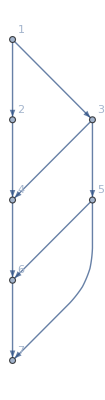
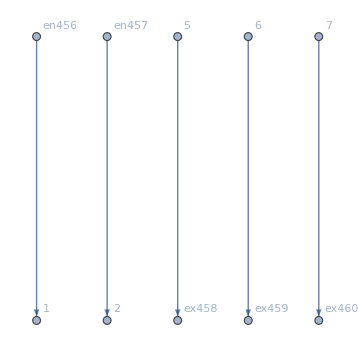
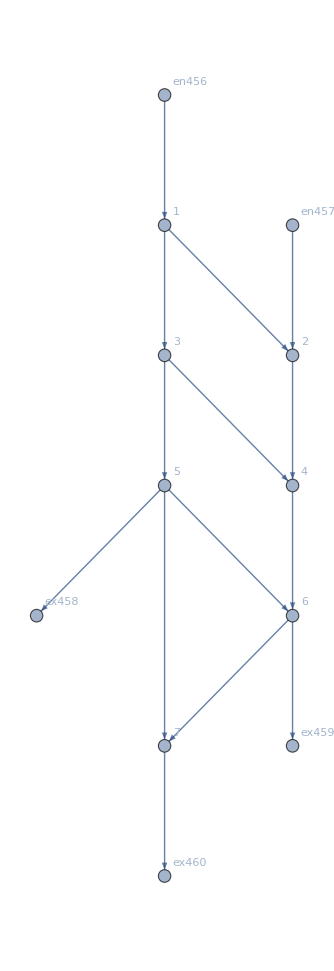
```mathematica
MFGEquations=<|"BG"->-Graphics-,"EntranceVertices"->{1,2},"InwardVertices"-><|1->en456,2->en457|>,"InEdges"->{en456->1,en457->2},"ExitVertices"->{5,6,7},"OutwardVertices"-><|5->ex458,6->ex459,7->ex460|>,"OutEdges"->{5->ex458,6->ex459,7->ex460},"AuxiliaryGraph"->-Graphics-,"FG"->-Graphics-,"VL"->{1,2,3,4,5,6,7},"EL"->{1->2,1->3,2->4,3->4,3->5,4->6,5->6,5->7,5->ex458,6->7,6->ex459,7->ex460,en456->1,en457->2},"BEL"->{1->2,1->3,2->4,3->4,3->5,4->6,5->6,5->7,6->7},"FVL"->{1,2,3,4,5,6,7,en456,en457,ex458,ex459,ex460},"AllTransitions"->{{1,1->2,1->3},{1,1->2,en456->1},{1,1->3,1->2},{1,1->3,en456->1},{1,en456->1,1->2},{1,en456->1,1->3},{2,1->2,2->4},{2,1->2,en457->2},{2,2->4,1->2},{2,2->4,en457->2},{2,en457->2,1->2},{2,en457->2,2->4},{3,1->3,3->4},{3,1->3,3->5},{3,3->4,1->3},{3,3->4,3->5},{3,3->5,1->3},{3,3->5,3->4},{4,2->4,3->4},{4,2->4,4->6},{4,3->4,2->4},{4,3->4,4->6},{4,4->6,2->4},{4,4->6,3->4},{5,3->5,5->6},{5,3->5,5->7},{5,3->5,5->ex458},{5,5->6,3->5},{5,5->6,5->7},{5,5->6,5->ex458},{5,5->7,3->5},{5,5->7,5->6},{5,5->7,5->ex458},{5,5->ex458,3->5},{5,5->ex458,5->6},{5,5->ex458,5->7},{6,4->6,5->6},{6,4->6,6->7},{6,4->6,6->ex459},{6,5->6,4->6},{6,5->6,6->7},{6,5->6,6->ex459},{6,6->7,4->6},{6,6->7,5->6},{6,6->7,6->ex459},{6,6->ex459,4->6},{6,6->ex459,5->6},{6,6->ex459,6->7},{7,5->7,6->7},{7,5->7,7->ex460},{7,6->7,5->7},{7,6->7,7->ex460},{7,7->ex460,5->7},{7,7->ex460,6->7}},"NoDeadEnds"->{{1,1->2},{1,1->3},{1,en456->1},{2,1->2},{2,2->4},{2,en457->2},{3,1->3},{3,3->4},{3,3->5},{4,2->4},{4,3->4},{4,4->6},{5,3->5},{5,5->6},{5,5->7},{5,5->ex458},{6,4->6},{6,5->6},{6,6->7},{6,6->ex459},{7,5->7},{7,6->7},{7,7->ex460}},"NoDeadStarts"->{{2,1->2},{3,1->3},{en456,en456->1},{1,1->2},{4,2->4},{en457,en457->2},{1,1->3},{4,3->4},{5,3->5},{2,2->4},{3,3->4},{6,4->6},{3,3->5},{6,5->6},{7,5->7},{ex458,5->ex458},{4,4->6},{5,5->6},{7,6->7},{ex459,6->ex459},{5,5->7},{6,6->7},{ex460,7->ex460}},"jargs"->{{2,1->2},{3,1->3},{4,2->4},{4,3->4},{5,3->5},{6,4->6},{6,5->6},{7,5->7},{ex458,5->ex458},{7,6->7},{ex459,6->ex459},{ex460,7->ex460},{1,en456->1},{2,en457->2},{1,1->2},{1,1->3},{2,2->4},{3,3->4},{3,3->5},{4,4->6},{5,5->6},{5,5->7},{5,5->ex458},{6,6->7},{6,6->ex459},{7,7->ex460},{en456,en456->1},{en457,en457->2}},"js"->{j461,j462,j463,j464,j465,j466,j467,j468,j469,j470,j471,j472,j473,j474,j475,j476,j477,j478,j479,j480,j481,j482,j483,j484,j485,j486,j487,j488},"jvars"-><|{2,1->2}->j461,{3,1->3}->j462,{4,2->4}->j463,{4,3->4}->j464,{5,3->5}->j465,{6,4->6}->j466,{6,5->6}->j467,{7,5->7}->j468,{ex458,5->ex458}->j469,{7,6->7}->j470,{ex459,6->ex459}->j471,{ex460,7->ex460}->j472,{1,en456->1}->j473,{2,en457->2}->j474,{1,1->2}->j475,{1,1->3}->j476,{2,2->4}->j477,{3,3->4}->j478,{3,3->5}->j479,{4,4->6}->j480,{5,5->6}->j481,{5,5->7}->j482,{5,5->ex458}->j483,{6,6->7}->j484,{6,6->ex459}->j485,{7,7->ex460}->j486,{en456,en456->1}->j487,{en457,en457->2}->j488|>,"jts"->{jt489,jt490,jt491,jt492,jt493,jt494,jt495,jt496,jt497,jt498,jt499,jt500,jt501,jt502,jt503,jt504,jt505,jt506,jt507,jt508,jt509,jt510,jt511,jt512,jt513,jt514,jt515,jt516,jt517,jt518,jt519,jt520,jt521,jt522,jt523,jt524,jt525,jt526,jt527,jt528,jt529,jt530,jt531,jt532,jt533,jt534,jt535,jt536,jt537,jt538,jt539,jt540,jt541,jt542},"jtvars"-><|{1,1->2,1->3}->jt489,{1,1->2,en456->1}->jt490,{1,1->3,1->2}->jt491,{1,1->3,en456->1}->jt492,{1,en456->1,1->2}->jt493,{1,en456->1,1->3}->jt494,{2,1->2,2->4}->jt495,{2,1->2,en457->2}->jt496,{2,2->4,1->2}->jt497,{2,2->4,en457->2}->jt498,{2,en457->2,1->2}->jt499,{2,en457->2,2->4}->jt500,{3,1->3,3->4}->jt501,{3,1->3,3->5}->jt502,{3,3->4,1->3}->jt503,{3,3->4,3->5}->jt504,{3,3->5,1->3}->jt505,{3,3->5,3->4}->jt506,{4,2->4,3->4}->jt507,{4,2->4,4->6}->jt508,{4,3->4,2->4}->jt509,{4,3->4,4->6}->jt510,{4,4->6,2->4}->jt511,{4,4->6,3->4}->jt512,{5,3->5,5->6}->jt513,{5,3->5,5->7}->jt514,{5,3->5,5->ex458}->jt515,{5,5->6,3->5}->jt516,{5,5->6,5->7}->jt517,{5,5->6,5->ex458}->jt518,{5,5->7,3->5}->jt519,{5,5->7,5->6}->jt520,{5,5->7,5->ex458}->jt521,{5,5->ex458,3->5}->jt522,{5,5->ex458,5->6}->jt523,{5,5->ex458,5->7}->jt524,{6,4->6,5->6}->jt525,{6,4->6,6->7}->jt526,{6,4->6,6->ex459}->jt527,{6,5->6,4->6}->jt528,{6,5->6,6->7}->jt529,{6,5->6,6->ex459}->jt530,{6,6->7,4->6}->jt531,{6,6->7,5->6}->jt532,{6,6->7,6->ex459}->jt533,{6,6->ex459,4->6}->jt534,{6,6->ex459,5->6}->jt535,{6,6->ex459,6->7}->jt536,{7,5->7,6->7}->jt537,{7,5->7,7->ex460}->jt538,{7,6->7,5->7}->jt539,{7,6->7,7->ex460}->jt540,{7,7->ex460,5->7}->jt541,{7,7->ex460,6->7}->jt542|>,"uargs"->{{1,1->2},{1,1->3},{2,2->4},{3,3->4},{3,3->5},{4,4->6},{5,5->6},{5,5->7},{5,5->ex458},{6,6->7},{6,6->ex459},{7,7->ex460},{en456,en456->1},{en457,en457->2},{2,1->2},{3,1->3},{4,2->4},{4,3->4},{5,3->5},{6,4->6},{6,5->6},{7,5->7},{ex458,5->ex458},{7,6->7},{ex459,6->ex459},{ex460,7->ex460},{1,en456->1},{2,en457->2}},"us"->{u543,u544,u545,u546,u547,u548,u549,u550,u551,u552,u553,u554,u555,u556,u557,u558,u559,u560,u561,u562,u563,u564,u565,u566,u567,u568,u569,u570},"uvars"-><|{1,1->2}->u543,{1,1->3}->u544,{2,2->4}->u545,{3,3->4}->u546,{3,3->5}->u547,{4,4->6}->u548,{5,5->6}->u549,{5,5->7}->u550,{5,5->ex458}->u551,{6,6->7}->u552,{6,6->ex459}->u553,{7,7->ex460}->u554,{en456,en456->1}->u555,{en457,en457->2}->u556,{2,1->2}->u557,{3,1->3}->u558,{4,2->4}->u559,{4,3->4}->u560,{5,3->5}->u561,{6,4->6}->u562,{6,5->6}->u563,{7,5->7}->u564,{ex458,5->ex458}->u565,{7,6->7}->u566,{ex459,6->ex459}->u567,{ex460,7->ex460}->u568,{1,en456->1}->u569,{2,en457->2}->u570|>,"SwitchingCosts"-><|{1,1->2,1->3}->0,{1,1->2,en456->1}->∞,{1,1->3,1->2}->0,{1,1->3,en456->1}->∞,{1,en456->1,1->2}->0,{1,en456->1,1->3}->0,{2,1->2,2->4}->0,{2,1->2,en457->2}->∞,{2,2->4,1->2}->0,{2,2->4,en457->2}->∞,{2,en457->2,1->2}->0,{2,en457->2,2->4}->0,{3,1->3,3->4}->0,{3,1->3,3->5}->0,{3,3->4,1->3}->0,{3,3->4,3->5}->0,{3,3->5,1->3}->0,{3,3->5,3->4}->0,{4,2->4,3->4}->0,{4,2->4,4->6}->0,{4,3->4,2->4}->0,{4,3->4,4->6}->0,{4,4->6,2->4}->0,{4,4->6,3->4}->0,{5,3->5,5->6}->0,{5,3->5,5->7}->0,{5,3->5,5->ex458}->0,{5,5->6,3->5}->0,{5,5->6,5->7}->0,{5,5->6,5->ex458}->0,{5,5->7,3->5}->0,{5,5->7,5->6}->0,{5,5->7,5->ex458}->0,{5,5->ex458,3->5}->∞,{5,5->ex458,5->6}->∞,{5,5->ex458,5->7}->∞,{6,4->6,5->6}->0,{6,4->6,6->7}->0,{6,4->6,6->ex459}->0,{6,5->6,4->6}->0,{6,5->6,6->7}->0,{6,5->6,6->ex459}->0,{6,6->7,4->6}->0,{6,6->7,5->6}->0,{6,6->7,6->ex459}->0,{6,6->ex459,4->6}->∞,{6,6->ex459,5->6}->∞,{6,6->ex459,6->7}->∞,{7,5->7,6->7}->0,{7,5->7,7->ex460}->0,{7,6->7,5->7}->0,{7,6->7,7->ex460}->0,{7,7->ex460,5->7}->∞,{7,7->ex460,6->7}->∞,{5,5->ex458,1->2}->∞,{5,5->ex458,1->3}->∞,{5,5->ex458,2->4}->∞,{5,5->ex458,3->4}->∞,{5,5->ex458,4->6}->∞,{5,5->ex458,5->ex458}->∞,{5,5->ex458,6->7}->∞,{5,5->ex458,6->ex459}->∞,{5,5->ex458,7->ex460}->∞,{5,5->ex458,en456->1}->∞,{5,5->ex458,en457->2}->∞,{6,6->ex459,1->2}->∞,{6,6->ex459,1->3}->∞,{6,6->ex459,2->4}->∞,{6,6->ex459,3->4}->∞,{6,6->ex459,3->5}->∞,{6,6->ex459,5->7}->∞,{6,6->ex459,5->ex458}->∞,{6,6->ex459,6->ex459}->∞,{6,6->ex459,7->ex460}->∞,{6,6->ex459,en456->1}->∞,{6,6->ex459,en457->2}->∞,{7,7->ex460,1->2}->∞,{7,7->ex460,1->3}->∞,{7,7->ex460,2->4}->∞,{7,7->ex460,3->4}->∞,{7,7->ex460,3->5}->∞,{7,7->ex460,4->6}->∞,{7,7->ex460,5->6}->∞,{7,7->ex460,5->ex458}->∞,{7,7->ex460,6->ex459}->∞,{7,7->ex460,7->ex460}->∞,{7,7->ex460,en456->1}->∞,{7,7->ex460,en457->2}->∞,{2,1->3,en457->2}->∞,{1,en456->1,en456->1}->∞,{2,en456->1,en457->2}->∞,{1,2->4,en456->1}->∞,{1,en457->2,en456->1}->∞,{2,en457->2,en457->2}->∞|>,"OutRules"->{{5,5->ex458,1->2}->∞,{5,5->ex458,1->3}->∞,{5,5->ex458,2->4}->∞,{5,5->ex458,3->4}->∞,{5,5->ex458,3->5}->∞,{5,5->ex458,4->6}->∞,{5,5->ex458,5->6}->∞,{5,5->ex458,5->7}->∞,{5,5->ex458,5->ex458}->∞,{5,5->ex458,6->7}->∞,{5,5->ex458,6->ex459}->∞,{5,5->ex458,7->ex460}->∞,{5,5->ex458,en456->1}->∞,{5,5->ex458,en457->2}->∞,{6,6->ex459,1->2}->∞,{6,6->ex459,1->3}->∞,{6,6->ex459,2->4}->∞,{6,6->ex459,3->4}->∞,{6,6->ex459,3->5}->∞,{6,6->ex459,4->6}->∞,{6,6->ex459,5->6}->∞,{6,6->ex459,5->7}->∞,{6,6->ex459,5->ex458}->∞,{6,6->ex459,6->7}->∞,{6,6->ex459,6->ex459}->∞,{6,6->ex459,7->ex460}->∞,{6,6->ex459,en456->1}->∞,{6,6->ex459,en457->2}->∞,{7,7->ex460,1->2}->∞,{7,7->ex460,1->3}->∞,{7,7->ex460,2->4}->∞,{7,7->ex460,3->4}->∞,{7,7->ex460,3->5}->∞,{7,7->ex460,4->6}->∞,{7,7->ex460,5->6}->∞,{7,7->ex460,5->7}->∞,{7,7->ex460,5->ex458}->∞,{7,7->ex460,6->7}->∞,{7,7->ex460,6->ex459}->∞,{7,7->ex460,7->ex460}->∞,{7,7->ex460,en456->1}->∞,{7,7->ex460,en457->2}->∞},"InRules"->{{1,1->2,en456->1}->∞,{2,1->2,en457->2}->∞,{1,1->3,en456->1}->∞,{2,1->3,en457->2}->∞,{1,en456->1,en456->1}->∞,{2,en456->1,en457->2}->∞,{1,1->2,en456->1}->∞,{2,1->2,en457->2}->∞,{1,2->4,en456->1}->∞,{2,2->4,en457->2}->∞,{1,en457->2,en456->1}->∞,{2,en457->2,en457->2}->∞},"EntryArgs"->{{1,en456->1},{2,en457->2}},"EntryDataAssociation"-><|{1,en456->1}->1,{2,en457->2}->2|>,"jays"-><|1->2->j461-j475,1->3->j462-j476,2->4->j463-j477,3->4->j464-j478,3->5->j465-j479,4->6->j466-j480,5->6->j467-j481,5->7->j468-j482,6->7->j470-j484|>,"NonZeroEntryCurrents"->True,"ExitCosts"-><|ex458->1,ex459->2,ex460->3|>,"EqCurrentCompCon"->(j475==0||j461==0)&&(j476==0||j462==0)&&(j477==0||j463==0)&&(j478==0||j464==0)&&(j479==0||j465==0)&&(j480==0||j466==0)&&(j481==0||j467==0)&&(j482==0||j468==0)&&(j483==0||j469==0)&&(j484==0||j470==0)&&(j485==0||j471==0)&&(j486==0||j472==0)&&(j487==0||j473==0)&&(j488==0||j474==0),"EqTransitionCompCon"->(jt489==0||jt491==0)&&(jt490==0||jt493==0)&&(jt492==0||jt494==0)&&(jt495==0||jt497==0)&&(jt496==0||jt499==0)&&(jt498==0||jt500==0)&&(jt501==0||jt503==0)&&(jt502==0||jt505==0)&&(jt504==0||jt506==0)&&(jt507==0||jt509==0)&&(jt508==0||jt511==0)&&(jt510==0||jt512==0)&&(jt513==0||jt516==0)&&(jt514==0||jt519==0)&&(jt515==0||jt522==0)&&(jt517==0||jt520==0)&&(jt518==0||jt523==0)&&(jt521==0||jt524==0)&&(jt525==0||jt528==0)&&(jt526==0||jt531==0)&&(jt527==0||jt534==0)&&(jt529==0||jt532==0)&&(jt530==0||jt535==0)&&(jt533==0||jt536==0)&&(jt537==0||jt539==0)&&(jt538==0||jt541==0)&&(jt540==0||jt542==0),"EqCompCon"->(jt489==0||-u543+u544==0)&&jt490==0&&(jt491==0||u543-u544==0)&&jt492==0&&(jt493==0||u543-u569==0)&&(jt494==0||u544-u569==0)&&(jt495==0||u545-u557==0)&&jt496==0&&(jt497==0||-u545+u557==0)&&jt498==0&&(jt499==0||u557-u570==0)&&(jt500==0||u545-u570==0)&&(jt501==0||u546-u558==0)&&(jt502==0||u547-u558==0)&&(jt503==0||-u546+u558==0)&&(jt504==0||-u546+u547==0)&&(jt505==0||-u547+u558==0)&&(jt506==0||u546-u547==0)&&(jt507==0||-u559+u560==0)&&(jt508==0||u548-u559==0)&&(jt509==0||u559-u560==0)&&(jt510==0||u548-u560==0)&&(jt511==0||-u548+u559==0)&&(jt512==0||-u548+u560==0)&&(jt513==0||u549-u561==0)&&(jt514==0||u550-u561==0)&&(jt515==0||u551-u561==0)&&(jt516==0||-u549+u561==0)&&(jt517==0||-u549+u550==0)&&(jt518==0||-u549+u551==0)&&(jt519==0||-u550+u561==0)&&(jt520==0||u549-u550==0)&&(jt521==0||-u550+u551==0)&&jt522==0&&jt523==0&&jt524==0&&(jt525==0||-u562+u563==0)&&(jt526==0||u552-u562==0)&&(jt527==0||u553-u562==0)&&(jt528==0||u562-u563==0)&&(jt529==0||u552-u563==0)&&(jt530==0||u553-u563==0)&&(jt531==0||-u552+u562==0)&&(jt532==0||-u552+u563==0)&&(jt533==0||-u552+u553==0)&&jt534==0&&jt535==0&&jt536==0&&(jt537==0||-u564+u566==0)&&(jt538==0||u554-u564==0)&&(jt539==0||u564-u566==0)&&(jt540==0||u554-u566==0)&&jt541==0&&jt542==0,"EqAllComp"->(j475==0||j461==0)&&(j476==0||j462==0)&&(j477==0||j463==0)&&(j478==0||j464==0)&&(j479==0||j465==0)&&(j480==0||j466==0)&&(j481==0||j467==0)&&(j482==0||j468==0)&&(j483==0||j469==0)&&(j484==0||j470==0)&&(j485==0||j471==0)&&(j486==0||j472==0)&&(j487==0||j473==0)&&(j488==0||j474==0)&&(jt489==0||jt491==0)&&(jt490==0||jt493==0)&&(jt492==0||jt494==0)&&(jt495==0||jt497==0)&&(jt496==0||jt499==0)&&(jt498==0||jt500==0)&&(jt501==0||jt503==0)&&(jt502==0||jt505==0)&&(jt504==0||jt506==0)&&(jt507==0||jt509==0)&&(jt508==0||jt511==0)&&(jt510==0||jt512==0)&&(jt513==0||jt516==0)&&(jt514==0||jt519==0)&&(jt515==0||jt522==0)&&(jt517==0||jt520==0)&&(jt518==0||jt523==0)&&(jt521==0||jt524==0)&&(jt525==0||jt528==0)&&(jt526==0||jt531==0)&&(jt527==0||jt534==0)&&(jt529==0||jt532==0)&&(jt530==0||jt535==0)&&(jt533==0||jt536==0)&&(jt537==0||jt539==0)&&(jt538==0||jt541==0)&&(jt540==0||jt542==0)&&(jt489==0||-u543+u544==0)&&jt490==0&&(jt491==0||u543-u544==0)&&jt492==0&&(jt493==0||u543-u569==0)&&(jt494==0||u544-u569==0)&&(jt495==0||u545-u557==0)&&jt496==0&&(jt497==0||-u545+u557==0)&&jt498==0&&(jt499==0||u557-u570==0)&&(jt500==0||u545-u570==0)&&(jt501==0||u546-u558==0)&&(jt502==0||u547-u558==0)&&(jt503==0||-u546+u558==0)&&(jt504==0||-u546+u547==0)&&(jt505==0||-u547+u558==0)&&(jt506==0||u546-u547==0)&&(jt507==0||-u559+u560==0)&&(jt508==0||u548-u559==0)&&(jt509==0||u559-u560==0)&&(jt510==0||u548-u560==0)&&(jt511==0||-u548+u559==0)&&(jt512==0||-u548+u560==0)&&(jt513==0||u549-u561==0)&&(jt514==0||u550-u561==0)&&(jt515==0||u551-u561==0)&&(jt516==0||-u549+u561==0)&&(jt517==0||-u549+u550==0)&&(jt518==0||-u549+u551==0)&&(jt519==0||-u550+u561==0)&&(jt520==0||u549-u550==0)&&(jt521==0||-u550+u551==0)&&jt522==0&&jt523==0&&jt524==0&&(jt525==0||-u562+u563==0)&&(jt526==0||u552-u562==0)&&(jt527==0||u553-u562==0)&&(jt528==0||u562-u563==0)&&(jt529==0||u552-u563==0)&&(jt530==0||u553-u563==0)&&(jt531==0||-u552+u562==0)&&(jt532==0||-u552+u563==0)&&(jt533==0||-u552+u553==0)&&jt534==0&&jt535==0&&jt536==0&&(jt537==0||-u564+u566==0)&&(jt538==0||u554-u564==0)&&(jt539==0||u564-u566==0)&&(jt540==0||u554-u566==0)&&jt541==0&&jt542==0,"EqPosCon"->NonNegative[j461]&&NonNegative[j462]&&NonNegative[j463]&&NonNegative[j464]&&NonNegative[j465]&&NonNegative[j466]&&NonNegative[j467]&&NonNegative[j468]&&NonNegative[j469]&&NonNegative[j470]&&NonNegative[j471]&&NonNegative[j472]&&NonNegative[j473]&&NonNegative[j474]&&NonNegative[j475]&&NonNegative[j476]&&NonNegative[j477]&&NonNegative[j478]&&NonNegative[j479]&&NonNegative[j480]&&NonNegative[j481]&&NonNegative[j482]&&NonNegative[j483]&&NonNegative[j484]&&NonNegative[j485]&&NonNegative[j486]&&NonNegative[j487]&&NonNegative[j488]&&NonNegative[jt489]&&NonNegative[jt490]&&NonNegative[jt491]&&NonNegative[jt492]&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&NonNegative[jt496]&&NonNegative[jt497]&&NonNegative[jt498]&&NonNegative[jt499]&&NonNegative[jt500]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[jt503]&&NonNegative[jt504]&&NonNegative[jt505]&&NonNegative[jt506]&&NonNegative[jt507]&&NonNegative[jt508]&&NonNegative[jt509]&&NonNegative[jt510]&&NonNegative[jt511]&&NonNegative[jt512]&&NonNegative[jt513]&&NonNegative[jt514]&&NonNegative[jt515]&&NonNegative[jt516]&&NonNegative[jt517]&&NonNegative[jt518]&&NonNegative[jt519]&&NonNegative[jt520]&&NonNegative[jt521]&&NonNegative[jt522]&&NonNegative[jt523]&&NonNegative[jt524]&&NonNegative[jt525]&&NonNegative[jt526]&&NonNegative[jt527]&&NonNegative[jt528]&&NonNegative[jt529]&&NonNegative[jt530]&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt533]&&NonNegative[jt534]&&NonNegative[jt535]&&NonNegative[jt536]&&NonNegative[jt537]&&NonNegative[jt538]&&NonNegative[jt539]&&NonNegative[jt540]&&NonNegative[jt541]&&NonNegative[jt542],"EqBalanceSplittingCurrents"->j475==jt489+jt490&&j476==jt491+jt492&&j473==jt493+jt494&&j461==jt495+jt496&&j477==jt497+jt498&&j474==jt499+jt500&&j462==jt501+jt502&&j478==jt503+jt504&&j479==jt505+jt506&&j463==jt507+jt508&&j464==jt509+jt510&&j480==jt511+jt512&&j465==jt513+jt514+jt515&&j481==jt516+jt517+jt518&&j482==jt519+jt520+jt521&&j483==jt522+jt523+jt524&&j466==jt525+jt526+jt527&&j467==jt528+jt529+jt530&&j484==jt531+jt532+jt533&&j485==jt534+jt535+jt536&&j468==jt537+jt538&&j470==jt539+jt540&&j486==jt541+jt542,"EqBalanceGatheringCurrents"->j461==jt491+jt493&&j462==jt489+jt494&&j487==jt490+jt492&&j475==jt497+jt499&&j463==jt495+jt500&&j488==jt496+jt498&&j476==jt503+jt505&&j464==jt501+jt506&&j465==jt502+jt504&&j477==jt509+jt511&&j478==jt507+jt512&&j466==jt508+jt510&&j479==jt516+jt519+jt522&&j467==jt513+jt520+jt523&&j468==jt514+jt517+jt524&&j469==jt515+jt518+jt521&&j480==jt528+jt531+jt534&&j481==jt525+jt532+jt535&&j470==jt526+jt529+jt536&&j471==jt527+jt530+jt533&&j482==jt539+jt541&&j484==jt537+jt542&&j472==jt538+jt540,"EqEntryIn"->j473==1&&j474==2,"EqExitValues"->u565==1&&u567==2&&u568==3,"EqSwitchingConditions"->NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u569]&&NonNegative[u544-u569]&&NonNegative[u545-u557]&&NonNegative[-u545+u557]&&NonNegative[u557-u570]&&NonNegative[u545-u570]&&NonNegative[u546-u558]&&NonNegative[u547-u558]&&NonNegative[-u546+u558]&&NonNegative[-u546+u547]&&NonNegative[-u547+u558]&&NonNegative[u546-u547]&&NonNegative[-u559+u560]&&NonNegative[u548-u559]&&NonNegative[u559-u560]&&NonNegative[u548-u560]&&NonNegative[-u548+u559]&&NonNegative[-u548+u560]&&NonNegative[u549-u561]&&NonNegative[u550-u561]&&NonNegative[u551-u561]&&NonNegative[-u549+u561]&&NonNegative[-u549+u550]&&NonNegative[-u549+u551]&&NonNegative[-u550+u561]&&NonNegative[u549-u550]&&NonNegative[-u550+u551]&&NonNegative[-u562+u563]&&NonNegative[u552-u562]&&NonNegative[u553-u562]&&NonNegative[u562-u563]&&NonNegative[u552-u563]&&NonNegative[u553-u563]&&NonNegative[-u552+u562]&&NonNegative[-u552+u563]&&NonNegative[-u552+u553]&&NonNegative[-u564+u566]&&NonNegative[u554-u564]&&NonNegative[u564-u566]&&NonNegative[u554-u566],"EqValueAuxiliaryEdges"->-u555+u569==0&&-u556+u570==0&&-u551+u565==0&&-u553+u567==0&&-u554+u568==0,"EqAll"->NonNegative[j461]&&NonNegative[j462]&&NonNegative[j463]&&NonNegative[j464]&&NonNegative[j465]&&NonNegative[j466]&&NonNegative[j467]&&NonNegative[j468]&&NonNegative[j469]&&NonNegative[j470]&&NonNegative[j471]&&NonNegative[j472]&&NonNegative[j473]&&NonNegative[j474]&&NonNegative[j475]&&NonNegative[j476]&&NonNegative[j477]&&NonNegative[j478]&&NonNegative[j479]&&NonNegative[j480]&&NonNegative[j481]&&NonNegative[j482]&&NonNegative[j483]&&NonNegative[j484]&&NonNegative[j485]&&NonNegative[j486]&&NonNegative[j487]&&NonNegative[j488]&&NonNegative[jt489]&&NonNegative[jt490]&&NonNegative[jt491]&&NonNegative[jt492]&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&NonNegative[jt496]&&NonNegative[jt497]&&NonNegative[jt498]&&NonNegative[jt499]&&NonNegative[jt500]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[jt503]&&NonNegative[jt504]&&NonNegative[jt505]&&NonNegative[jt506]&&NonNegative[jt507]&&NonNegative[jt508]&&NonNegative[jt509]&&NonNegative[jt510]&&NonNegative[jt511]&&NonNegative[jt512]&&NonNegative[jt513]&&NonNegative[jt514]&&NonNegative[jt515]&&NonNegative[jt516]&&NonNegative[jt517]&&NonNegative[jt518]&&NonNegative[jt519]&&NonNegative[jt520]&&NonNegative[jt521]&&NonNegative[jt522]&&NonNegative[jt523]&&NonNegative[jt524]&&NonNegative[jt525]&&NonNegative[jt526]&&NonNegative[jt527]&&NonNegative[jt528]&&NonNegative[jt529]&&NonNegative[jt530]&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt533]&&NonNegative[jt534]&&NonNegative[jt535]&&NonNegative[jt536]&&NonNegative[jt537]&&NonNegative[jt538]&&NonNegative[jt539]&&NonNegative[jt540]&&NonNegative[jt541]&&NonNegative[jt542]&&j475==jt489+jt490&&j476==jt491+jt492&&j473==jt493+jt494&&j461==jt495+jt496&&j477==jt497+jt498&&j474==jt499+jt500&&j462==jt501+jt502&&j478==jt503+jt504&&j479==jt505+jt506&&j463==jt507+jt508&&j464==jt509+jt510&&j480==jt511+jt512&&j465==jt513+jt514+jt515&&j481==jt516+jt517+jt518&&j482==jt519+jt520+jt521&&j483==jt522+jt523+jt524&&j466==jt525+jt526+jt527&&j467==jt528+jt529+jt530&&j484==jt531+jt532+jt533&&j485==jt534+jt535+jt536&&j468==jt537+jt538&&j470==jt539+jt540&&j486==jt541+jt542&&j461==jt491+jt493&&j462==jt489+jt494&&j487==jt490+jt492&&j475==jt497+jt499&&j463==jt495+jt500&&j488==jt496+jt498&&j476==jt503+jt505&&j464==jt501+jt506&&j465==jt502+jt504&&j477==jt509+jt511&&j478==jt507+jt512&&j466==jt508+jt510&&j479==jt516+jt519+jt522&&j467==jt513+jt520+jt523&&j468==jt514+jt517+jt524&&j469==jt515+jt518+jt521&&j480==jt528+jt531+jt534&&j481==jt525+jt532+jt535&&j470==jt526+jt529+jt536&&j471==jt527+jt530+jt533&&j482==jt539+jt541&&j484==jt537+jt542&&j472==jt538+jt540&&j473==1&&j474==2&&u565==1&&u567==2&&u568==3&&NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u569]&&NonNegative[u544-u569]&&NonNegative[u545-u557]&&NonNegative[-u545+u557]&&NonNegative[u557-u570]&&NonNegative[u545-u570]&&NonNegative[u546-u558]&&NonNegative[u547-u558]&&NonNegative[-u546+u558]&&NonNegative[-u546+u547]&&NonNegative[-u547+u558]&&NonNegative[u546-u547]&&NonNegative[-u559+u560]&&NonNegative[u548-u559]&&NonNegative[u559-u560]&&NonNegative[u548-u560]&&NonNegative[-u548+u559]&&NonNegative[-u548+u560]&&NonNegative[u549-u561]&&NonNegative[u550-u561]&&NonNegative[u551-u561]&&NonNegative[-u549+u561]&&NonNegative[-u549+u550]&&NonNegative[-u549+u551]&&NonNegative[-u550+u561]&&NonNegative[u549-u550]&&NonNegative[-u550+u551]&&NonNegative[-u562+u563]&&NonNegative[u552-u562]&&NonNegative[u553-u562]&&NonNegative[u562-u563]&&NonNegative[u552-u563]&&NonNegative[u553-u563]&&NonNegative[-u552+u562]&&NonNegative[-u552+u563]&&NonNegative[-u552+u553]&&NonNegative[-u564+u566]&&NonNegative[u554-u564]&&NonNegative[u564-u566]&&NonNegative[u554-u566]&&-u555+u569==0&&-u556+u570==0&&-u551+u565==0&&-u553+u567==0&&-u554+u568==0,"EqAllAll"->NonNegative[j461]&&NonNegative[j462]&&NonNegative[j463]&&NonNegative[j464]&&NonNegative[j465]&&NonNegative[j466]&&NonNegative[j467]&&NonNegative[j468]&&NonNegative[j469]&&NonNegative[j470]&&NonNegative[j471]&&NonNegative[j472]&&NonNegative[j473]&&NonNegative[j474]&&NonNegative[j475]&&NonNegative[j476]&&NonNegative[j477]&&NonNegative[j478]&&NonNegative[j479]&&NonNegative[j480]&&NonNegative[j481]&&NonNegative[j482]&&NonNegative[j483]&&NonNegative[j484]&&NonNegative[j485]&&NonNegative[j486]&&NonNegative[j487]&&NonNegative[j488]&&NonNegative[jt489]&&NonNegative[jt490]&&NonNegative[jt491]&&NonNegative[jt492]&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&NonNegative[jt496]&&NonNegative[jt497]&&NonNegative[jt498]&&NonNegative[jt499]&&NonNegative[jt500]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[jt503]&&NonNegative[jt504]&&NonNegative[jt505]&&NonNegative[jt506]&&NonNegative[jt507]&&NonNegative[jt508]&&NonNegative[jt509]&&NonNegative[jt510]&&NonNegative[jt511]&&NonNegative[jt512]&&NonNegative[jt513]&&NonNegative[jt514]&&NonNegative[jt515]&&NonNegative[jt516]&&NonNegative[jt517]&&NonNegative[jt518]&&NonNegative[jt519]&&NonNegative[jt520]&&NonNegative[jt521]&&NonNegative[jt522]&&NonNegative[jt523]&&NonNegative[jt524]&&NonNegative[jt525]&&NonNegative[jt526]&&NonNegative[jt527]&&NonNegative[jt528]&&NonNegative[jt529]&&NonNegative[jt530]&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt533]&&NonNegative[jt534]&&NonNegative[jt535]&&NonNegative[jt536]&&NonNegative[jt537]&&NonNegative[jt538]&&NonNegative[jt539]&&NonNegative[jt540]&&NonNegative[jt541]&&NonNegative[jt542]&&j475==jt489+jt490&&j476==jt491+jt492&&j473==jt493+jt494&&j461==jt495+jt496&&j477==jt497+jt498&&j474==jt499+jt500&&j462==jt501+jt502&&j478==jt503+jt504&&j479==jt505+jt506&&j463==jt507+jt508&&j464==jt509+jt510&&j480==jt511+jt512&&j465==jt513+jt514+jt515&&j481==jt516+jt517+jt518&&j482==jt519+jt520+jt521&&j483==jt522+jt523+jt524&&j466==jt525+jt526+jt527&&j467==jt528+jt529+jt530&&j484==jt531+jt532+jt533&&j485==jt534+jt535+jt536&&j468==jt537+jt538&&j470==jt539+jt540&&j486==jt541+jt542&&j461==jt491+jt493&&j462==jt489+jt494&&j487==jt490+jt492&&j475==jt497+jt499&&j463==jt495+jt500&&j488==jt496+jt498&&j476==jt503+jt505&&j464==jt501+jt506&&j465==jt502+jt504&&j477==jt509+jt511&&j478==jt507+jt512&&j466==jt508+jt510&&j479==jt516+jt519+jt522&&j467==jt513+jt520+jt523&&j468==jt514+jt517+jt524&&j469==jt515+jt518+jt521&&j480==jt528+jt531+jt534&&j481==jt525+jt532+jt535&&j470==jt526+jt529+jt536&&j471==jt527+jt530+jt533&&j482==jt539+jt541&&j484==jt537+jt542&&j472==jt538+jt540&&j473==1&&j474==2&&u565==1&&u567==2&&u568==3&&NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u569]&&NonNegative[u544-u569]&&NonNegative[u545-u557]&&NonNegative[-u545+u557]&&NonNegative[u557-u570]&&NonNegative[u545-u570]&&NonNegative[u546-u558]&&NonNegative[u547-u558]&&NonNegative[-u546+u558]&&NonNegative[-u546+u547]&&NonNegative[-u547+u558]&&NonNegative[u546-u547]&&NonNegative[-u559+u560]&&NonNegative[u548-u559]&&NonNegative[u559-u560]&&NonNegative[u548-u560]&&NonNegative[-u548+u559]&&NonNegative[-u548+u560]&&NonNegative[u549-u561]&&NonNegative[u550-u561]&&NonNegative[u551-u561]&&NonNegative[-u549+u561]&&NonNegative[-u549+u550]&&NonNegative[-u549+u551]&&NonNegative[-u550+u561]&&NonNegative[u549-u550]&&NonNegative[-u550+u551]&&NonNegative[-u562+u563]&&NonNegative[u552-u562]&&NonNegative[u553-u562]&&NonNegative[u562-u563]&&NonNegative[u552-u563]&&NonNegative[u553-u563]&&NonNegative[-u552+u562]&&NonNegative[-u552+u563]&&NonNegative[-u552+u553]&&NonNegative[-u564+u566]&&NonNegative[u554-u564]&&NonNegative[u564-u566]&&NonNegative[u554-u566]&&-u555+u569==0&&-u556+u570==0&&-u551+u565==0&&-u553+u567==0&&-u554+u568==0&&(j475==0||j461==0)&&(j476==0||j462==0)&&(j477==0||j463==0)&&(j478==0||j464==0)&&(j479==0||j465==0)&&(j480==0||j466==0)&&(j481==0||j467==0)&&(j482==0||j468==0)&&(j483==0||j469==0)&&(j484==0||j470==0)&&(j485==0||j471==0)&&(j486==0||j472==0)&&(j487==0||j473==0)&&(j488==0||j474==0)&&(jt489==0||jt491==0)&&(jt490==0||jt493==0)&&(jt492==0||jt494==0)&&(jt495==0||jt497==0)&&(jt496==0||jt499==0)&&(jt498==0||jt500==0)&&(jt501==0||jt503==0)&&(jt502==0||jt505==0)&&(jt504==0||jt506==0)&&(jt507==0||jt509==0)&&(jt508==0||jt511==0)&&(jt510==0||jt512==0)&&(jt513==0||jt516==0)&&(jt514==0||jt519==0)&&(jt515==0||jt522==0)&&(jt517==0||jt520==0)&&(jt518==0||jt523==0)&&(jt521==0||jt524==0)&&(jt525==0||jt528==0)&&(jt526==0||jt531==0)&&(jt527==0||jt534==0)&&(jt529==0||jt532==0)&&(jt530==0||jt535==0)&&(jt533==0||jt536==0)&&(jt537==0||jt539==0)&&(jt538==0||jt541==0)&&(jt540==0||jt542==0)&&(jt489==0||-u543+u544==0)&&jt490==0&&(jt491==0||u543-u544==0)&&jt492==0&&(jt493==0||u543-u569==0)&&(jt494==0||u544-u569==0)&&(jt495==0||u545-u557==0)&&jt496==0&&(jt497==0||-u545+u557==0)&&jt498==0&&(jt499==0||u557-u570==0)&&(jt500==0||u545-u570==0)&&(jt501==0||u546-u558==0)&&(jt502==0||u547-u558==0)&&(jt503==0||-u546+u558==0)&&(jt504==0||-u546+u547==0)&&(jt505==0||-u547+u558==0)&&(jt506==0||u546-u547==0)&&(jt507==0||-u559+u560==0)&&(jt508==0||u548-u559==0)&&(jt509==0||u559-u560==0)&&(jt510==0||u548-u560==0)&&(jt511==0||-u548+u559==0)&&(jt512==0||-u548+u560==0)&&(jt513==0||u549-u561==0)&&(jt514==0||u550-u561==0)&&(jt515==0||u551-u561==0)&&(jt516==0||-u549+u561==0)&&(jt517==0||-u549+u550==0)&&(jt518==0||-u549+u551==0)&&(jt519==0||-u550+u561==0)&&(jt520==0||u549-u550==0)&&(jt521==0||-u550+u551==0)&&jt522==0&&jt523==0&&jt524==0&&(jt525==0||-u562+u563==0)&&(jt526==0||u552-u562==0)&&(jt527==0||u553-u562==0)&&(jt528==0||u562-u563==0)&&(jt529==0||u552-u563==0)&&(jt530==0||u553-u563==0)&&(jt531==0||-u552+u562==0)&&(jt532==0||-u552+u563==0)&&(jt533==0||-u552+u553==0)&&jt534==0&&jt535==0&&jt536==0&&(jt537==0||-u564+u566==0)&&(jt538==0||u554-u564==0)&&(jt539==0||u564-u566==0)&&(jt540==0||u554-u566==0)&&jt541==0&&jt542==0,"BoundaryRules"->{j473->1,j474->2,u565->1,u567->2,u568->3},"RulesEntryIn"->{j473->1,j474->2},"RulesExitValues"->{u565->1,u567->2,u568->3},"Nlhs"->{j461-j475-u543+u557,j462-j476-u544+u558,j463-j477-u545+u559,j464-j478-u546+u560,j465-j479-u547+u561,j466-j480-u548+u562,j467-j481-u549+u563,j468-j482-u550+u564,j470-j484-u552+u566},"EqCriticalCase"->j461-j475-u543+u557==0&&j462-j476-u544+u558==0&&j463-j477-u545+u559==0&&j464-j478-u546+u560==0&&j465-j479-u547+u561==0&&j466-j480-u548+u562==0&&j467-j481-u549+u563==0&&j468-j482-u550+u564==0&&j470-j484-u552+u566==0,"criticalreduced1"->{True,<|j461->0,j462->59/41,j465->72/41,j469->3,j472->0,j473->1,j474->2,j475->18/41,j476->0,j477->0,j478->13/41,j479->0,j481->34/41,j482->17/41,j483->0,j485->0,j486->0,j487->0,j488->0,jt489->18/41,jt490->0,jt491->0,jt492->0,jt493->0,jt494->1,jt496->0,jt497->0,jt498->0,jt499->18/41,jt500->64/41,jt503->0,jt504->13/41,jt505->0,jt506->0,jt507->13/41,jt509->0,jt510->0,jt512->0,jt515->72/41,jt517->0,jt518->34/41,jt520->0,jt521->17/41,jt522->0,jt523->0,jt524->0,jt525->34/41,jt527->0,jt528->0,jt529->0,jt530->0,jt533->0,jt534->0,jt535->0,jt536->0,jt537->0,jt538->0,jt540->0,jt541->0,jt542->0,u551->1,u553->2,u554->3,u557->190/41,u558->113/41,u559->126/41,u560->126/41,u561->1,u562->75/41,u563->75/41,u564->58/41,u565->1,u566->58/41,u567->2,u568->3,u569->172/41,u570->190/41,j463->64/41,j464->0,j466->51/41,j467->0,j468->0,j470->17/41,j471->0,j480->0,j484->0,jt495->0,jt501->0,jt502->59/41,jt508->51/41,jt511->0,jt513->0,jt514->0,jt516->0,jt519->0,jt526->17/41,jt531->0,jt532->0,jt539->17/41,u543->172/41,u544->172/41,u545->190/41,u546->113/41,u547->113/41,u548->126/41,u549->1,u550->1,u552->75/41,u555->172/41,u556->190/41|>},"Nrhs"->{j461-j475+IntM[j461-j475,1->2],j462-j476+IntM[j462-j476,1->3],j463-j477+IntM[j463-j477,2->4],j464-j478+IntM[j464-j478,3->4],j465-j479+IntM[j465-j479,3->5],j466-j480+IntM[j466-j480,4->6],j467-j481+IntM[j467-j481,5->6],j468-j482+IntM[j468-j482,5->7],j470-j484+IntM[j470-j484,6->7]},"EqGeneralCase"->j461-j475-u543+u557==j461-j475+IntM[j461-j475,1->2]&&j462-j476-u544+u558==j462-j476+IntM[j462-j476,1->3]&&j463-j477-u545+u559==j463-j477+IntM[j463-j477,2->4]&&j464-j478-u546+u560==j464-j478+IntM[j464-j478,3->4]&&j465-j479-u547+u561==j465-j479+IntM[j465-j479,3->5]&&j466-j480-u548+u562==j466-j480+IntM[j466-j480,4->6]&&j467-j481-u549+u563==j467-j481+IntM[j467-j481,5->6]&&j468-j482-u550+u564==j468-j482+IntM[j468-j482,5->7]&&j470-j484-u552+u566==j470-j484+IntM[j470-j484,6->7],"TOL"->1/1000000|>;
```

```mathematica
unsortedsys=MFGEquations["EqAllAll"]&&MFGEquations["EqCriticalCase"]
```

NonNegative[j461]&&NonNegative[j462]&&NonNegative[j463]&&NonNegative[j464]&&NonNegative[j465]&&NonNegative[j466]&&NonNegative[j467]&&NonNegative[j468]&&NonNegative[j469]&&NonNegative[j470]&&NonNegative[j471]&&NonNegative[j472]&&NonNegative[j473]&&NonNegative[j474]&&NonNegative[j475]&&NonNegative[j476]&&NonNegative[j477]&&NonNegative[j478]&&NonNegative[j479]&&NonNegative[j480]&&NonNegative[j481]&&NonNegative[j482]&&NonNegative[j483]&&NonNegative[j484]&&NonNegative[j485]&&NonNegative[j486]&&NonNegative[j487]&&NonNegative[j488]&&NonNegative[jt489]&&NonNegative[jt490]&&NonNegative[jt491]&&NonNegative[jt492]&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&NonNegative[jt496]&&NonNegative[jt497]&&NonNegative[jt498]&&NonNegative[jt499]&&NonNegative[jt500]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[jt503]&&NonNegative[jt504]&&NonNegative[jt505]&&NonNegative[jt506]&&NonNegative[jt507]&&NonNegative[jt508]&&NonNegative[jt509]&&NonNegative[jt510]&&NonNegative[jt511]&&NonNegative[jt512]&&NonNegative[jt513]&&NonNegative[jt514]&&NonNegative[jt515]&&NonNegative[jt516]&&NonNegative[jt517]&&NonNegative[jt518]&&NonNegative[jt519]&&NonNegative[jt520]&&NonNegative[jt521]&&NonNegative[jt522]&&NonNegative[jt523]&&NonNegative[jt524]&&NonNegative[jt525]&&NonNegative[jt526]&&NonNegative[jt527]&&NonNegative[jt528]&&NonNegative[jt529]&&NonNegative[jt530]&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt533]&&NonNegative[jt534]&&NonNegative[jt535]&&NonNegative[jt536]&&NonNegative[jt537]&&NonNegative[jt538]&&NonNegative[jt539]&&NonNegative[jt540]&&NonNegative[jt541]&&NonNegative[jt542]&&j475==jt489+jt490&&j476==jt491+jt492&&j473==jt493+jt494&&j461==jt495+jt496&&j477==jt497+jt498&&j474==jt499+jt500&&j462==jt501+jt502&&j478==jt503+jt504&&j479==jt505+jt506&&j463==jt507+jt508&&j464==jt509+jt510&&j480==jt511+jt512&&j465==jt513+jt514+jt515&&j481==jt516+jt517+jt518&&j482==jt519+jt520+jt521&&j483==jt522+jt523+jt524&&j466==jt525+jt526+jt527&&j467==jt528+jt529+jt530&&j484==jt531+jt532+jt533&&j485==jt534+jt535+jt536&&j468==jt537+jt538&&j470==jt539+jt540&&j486==jt541+jt542&&j461==jt491+jt493&&j462==jt489+jt494&&j487==jt490+jt492&&j475==jt497+jt499&&j463==jt495+jt500&&j488==jt496+jt498&&j476==jt503+jt505&&j464==jt501+jt506&&j465==jt502+jt504&&j477==jt509+jt511&&j478==jt507+jt512&&j466==jt508+jt510&&j479==jt516+jt519+jt522&&j467==jt513+jt520+jt523&&j468==jt514+jt517+jt524&&j469==jt515+jt518+jt521&&j480==jt528+jt531+jt534&&j481==jt525+jt532+jt535&&j470==jt526+jt529+jt536&&j471==jt527+jt530+jt533&&j482==jt539+jt541&&j484==jt537+jt542&&j472==jt538+jt540&&j473==1&&j474==2&&u565==1&&u567==2&&u568==3&&NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u569]&&NonNegative[u544-u569]&&NonNegative[u545-u557]&&NonNegative[-u545+u557]&&NonNegative[u557-u570]&&NonNegative[u545-u570]&&NonNegative[u546-u558]&&NonNegative[u547-u558]&&NonNegative[-u546+u558]&&NonNegative[-u546+u547]&&NonNegative[-u547+u558]&&NonNegative[u546-u547]&&NonNegative[-u559+u560]&&NonNegative[u548-u559]&&NonNegative[u559-u560]&&NonNegative[u548-u560]&&NonNegative[-u548+u559]&&NonNegative[-u548+u560]&&NonNegative[u549-u561]&&NonNegative[u550-u561]&&NonNegative[u551-u561]&&NonNegative[-u549+u561]&&NonNegative[-u549+u550]&&NonNegative[-u549+u551]&&NonNegative[-u550+u561]&&NonNegative[u549-u550]&&NonNegative[-u550+u551]&&NonNegative[-u562+u563]&&NonNegative[u552-u562]&&NonNegative[u553-u562]&&NonNegative[u562-u563]&&NonNegative[u552-u563]&&NonNegative[u553-u563]&&NonNegative[-u552+u562]&&NonNegative[-u552+u563]&&NonNegative[-u552+u553]&&NonNegative[-u564+u566]&&NonNegative[u554-u564]&&NonNegative[u564-u566]&&NonNegative[u554-u566]&&-u555+u569==0&&-u556+u570==0&&-u551+u565==0&&-u553+u567==0&&-u554+u568==0&&(j475==0||j461==0)&&(j476==0||j462==0)&&(j477==0||j463==0)&&(j478==0||j464==0)&&(j479==0||j465==0)&&(j480==0||j466==0)&&(j481==0||j467==0)&&(j482==0||j468==0)&&(j483==0||j469==0)&&(j484==0||j470==0)&&(j485==0||j471==0)&&(j486==0||j472==0)&&(j487==0||j473==0)&&(j488==0||j474==0)&&(jt489==0||jt491==0)&&(jt490==0||jt493==0)&&(jt492==0||jt494==0)&&(jt495==0||jt497==0)&&(jt496==0||jt499==0)&&(jt498==0||jt500==0)&&(jt501==0||jt503==0)&&(jt502==0||jt505==0)&&(jt504==0||jt506==0)&&(jt507==0||jt509==0)&&(jt508==0||jt511==0)&&(jt510==0||jt512==0)&&(jt513==0||jt516==0)&&(jt514==0||jt519==0)&&(jt515==0||jt522==0)&&(jt517==0||jt520==0)&&(jt518==0||jt523==0)&&(jt521==0||jt524==0)&&(jt525==0||jt528==0)&&(jt526==0||jt531==0)&&(jt527==0||jt534==0)&&(jt529==0||jt532==0)&&(jt530==0||jt535==0)&&(jt533==0||jt536==0)&&(jt537==0||jt539==0)&&(jt538==0||jt541==0)&&(jt540==0||jt542==0)&&(jt489==0||-u543+u544==0)&&jt490==0&&(jt491==0||u543-u544==0)&&jt492==0&&(jt493==0||u543-u569==0)&&(jt494==0||u544-u569==0)&&(jt495==0||u545-u557==0)&&jt496==0&&(jt497==0||-u545+u557==0)&&jt498==0&&(jt499==0||u557-u570==0)&&(jt500==0||u545-u570==0)&&(jt501==0||u546-u558==0)&&(jt502==0||u547-u558==0)&&(jt503==0||-u546+u558==0)&&(jt504==0||-u546+u547==0)&&(jt505==0||-u547+u558==0)&&(jt506==0||u546-u547==0)&&(jt507==0||-u559+u560==0)&&(jt508==0||u548-u559==0)&&(jt509==0||u559-u560==0)&&(jt510==0||u548-u560==0)&&(jt511==0||-u548+u559==0)&&(jt512==0||-u548+u560==0)&&(jt513==0||u549-u561==0)&&(jt514==0||u550-u561==0)&&(jt515==0||u551-u561==0)&&(jt516==0||-u549+u561==0)&&(jt517==0||-u549+u550==0)&&(jt518==0||-u549+u551==0)&&(jt519==0||-u550+u561==0)&&(jt520==0||u549-u550==0)&&(jt521==0||-u550+u551==0)&&jt522==0&&jt523==0&&jt524==0&&(jt525==0||-u562+u563==0)&&(jt526==0||u552-u562==0)&&(jt527==0||u553-u562==0)&&(jt528==0||u562-u563==0)&&(jt529==0||u552-u563==0)&&(jt530==0||u553-u563==0)&&(jt531==0||-u552+u562==0)&&(jt532==0||-u552+u563==0)&&(jt533==0||-u552+u553==0)&&jt534==0&&jt535==0&&jt536==0&&(jt537==0||-u564+u566==0)&&(jt538==0||u554-u564==0)&&(jt539==0||u564-u566==0)&&(jt540==0||u554-u566==0)&&jt541==0&&jt542==0&&j461-j475-u543+u557==0&&j462-j476-u544+u558==0&&j463-j477-u545+u559==0&&j464-j478-u546+u560==0&&j465-j479-u547+u561==0&&j466-j480-u548+u562==0&&j467-j481-u549+u563==0&&j468-j482-u550+u564==0&&j470-j484-u552+u566==0

```mathematica
vars=Join[us,js,jts]
```

{u543,u544,u545,u546,u547,u548,u549,u550,u551,u552,u553,u554,u555,u556,u557,u558,u559,u560,u561,u562,u563,u564,u565,u566,u567,u568,u569,u570,j461,j462,j463,j464,j465,j466,j467,j468,j469,j470,j471,j472,j473,j474,j475,j476,j477,j478,j479,j480,j481,j482,j483,j484,j485,j486,j487,j488,jt489,jt490,jt491,jt492,jt493,jt494,jt495,jt496,jt497,jt498,jt499,jt500,jt501,jt502,jt503,jt504,jt505,jt506,jt507,jt508,jt509,jt510,jt511,jt512,jt513,jt514,jt515,jt516,jt517,jt518,jt519,jt520,jt521,jt522,jt523,jt524,jt525,jt526,jt527,jt528,jt529,jt530,jt531,jt532,jt533,jt534,jt535,jt536,jt537,jt538,jt539,jt540,jt541,jt542}

```mathematica
sortedsys=SortAnds[unsortedsys,vars]//AbsoluteTiming
```

{0.041317,NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u569]&&(jt489==0||-u543+u544==0)&&(jt491==0||u543-u544==0)&&(jt493==0||u543-u569==0)&&j461-j475-u543+u557==0&&NonNegative[u544-u569]&&(jt494==0||u544-u569==0)&&j462-j476-u544+u558==0&&NonNegative[u545-u557]&&NonNegative[-u545+u557]&&NonNegative[u545-u570]&&(jt495==0||u545-u557==0)&&(jt497==0||-u545+u557==0)&&(jt500==0||u545-u570==0)&&j463-j477-u545+u559==0&&NonNegative[u546-u558]&&NonNegative[-u546+u558]&&NonNegative[-u546+u547]&&NonNegative[u546-u547]&&(jt501==0||u546-u558==0)&&(jt503==0||-u546+u558==0)&&(jt504==0||-u546+u547==0)&&(jt506==0||u546-u547==0)&&j464-j478-u546+u560==0&&NonNegative[u547-u558]&&NonNegative[-u547+u558]&&(jt502==0||u547-u558==0)&&(jt505==0||-u547+u558==0)&&j465-j479-u547+u561==0&&NonNegative[u548-u559]&&NonNegative[u548-u560]&&NonNegative[-u548+u559]&&NonNegative[-u548+u560]&&(jt508==0||u548-u559==0)&&(jt510==0||u548-u560==0)&&(jt511==0||-u548+u559==0)&&(jt512==0||-u548+u560==0)&&j466-j480-u548+u562==0&&NonNegative[u549-u561]&&NonNegative[-u549+u561]&&NonNegative[-u549+u550]&&NonNegative[-u549+u551]&&NonNegative[u549-u550]&&(jt513==0||u549-u561==0)&&(jt516==0||-u549+u561==0)&&(jt517==0||-u549+u550==0)&&(jt518==0||-u549+u551==0)&&(jt520==0||u549-u550==0)&&j467-j481-u549+u563==0&&NonNegative[u550-u561]&&NonNegative[-u550+u561]&&NonNegative[-u550+u551]&&(jt514==0||u550-u561==0)&&(jt519==0||-u550+u561==0)&&(jt521==0||-u550+u551==0)&&j468-j482-u550+u564==0&&NonNegative[u551-u561]&&-u551+u565==0&&(jt515==0||u551-u561==0)&&NonNegative[u552-u562]&&NonNegative[u552-u563]&&NonNegative[-u552+u562]&&NonNegative[-u552+u563]&&NonNegative[-u552+u553]&&(jt526==0||u552-u562==0)&&(jt529==0||u552-u563==0)&&(jt531==0||-u552+u562==0)&&(jt532==0||-u552+u563==0)&&(jt533==0||-u552+u553==0)&&j470-j484-u552+u566==0&&NonNegative[u553-u562]&&NonNegative[u553-u563]&&-u553+u567==0&&(jt527==0||u553-u562==0)&&(jt530==0||u553-u563==0)&&NonNegative[u554-u564]&&NonNegative[u554-u566]&&-u554+u568==0&&(jt538==0||u554-u564==0)&&(jt540==0||u554-u566==0)&&-u555+u569==0&&-u556+u570==0&&NonNegative[u557-u570]&&(jt499==0||u557-u570==0)&&NonNegative[-u559+u560]&&NonNegative[u559-u560]&&(jt507==0||-u559+u560==0)&&(jt509==0||u559-u560==0)&&NonNegative[-u562+u563]&&NonNegative[u562-u563]&&(jt525==0||-u562+u563==0)&&(jt528==0||u562-u563==0)&&NonNegative[-u564+u566]&&NonNegative[u564-u566]&&(jt537==0||-u564+u566==0)&&(jt539==0||u564-u566==0)&&u565==1&&u567==2&&u568==3&&NonNegative[j461]&&j461==jt495+jt496&&j461==jt491+jt493&&(j475==0||j461==0)&&NonNegative[j462]&&j462==jt501+jt502&&j462==jt489+jt494&&(j476==0||j462==0)&&NonNegative[j463]&&j463==jt507+jt508&&j463==jt495+jt500&&(j477==0||j463==0)&&NonNegative[j464]&&j464==jt509+jt510&&j464==jt501+jt506&&(j478==0||j464==0)&&NonNegative[j465]&&j465==jt513+jt514+jt515&&j465==jt502+jt504&&(j479==0||j465==0)&&NonNegative[j466]&&j466==jt525+jt526+jt527&&j466==jt508+jt510&&(j480==0||j466==0)&&NonNegative[j467]&&j467==jt528+jt529+jt530&&j467==jt513+jt520+jt523&&(j481==0||j467==0)&&NonNegative[j468]&&j468==jt537+jt538&&j468==jt514+jt517+jt524&&(j482==0||j468==0)&&NonNegative[j469]&&j469==jt515+jt518+jt521&&(j483==0||j469==0)&&NonNegative[j470]&&j470==jt539+jt540&&j470==jt526+jt529+jt536&&(j484==0||j470==0)&&NonNegative[j471]&&j471==jt527+jt530+jt533&&(j485==0||j471==0)&&NonNegative[j472]&&j472==jt538+jt540&&(j486==0||j472==0)&&NonNegative[j473]&&j473==jt493+jt494&&j473==1&&(j487==0||j473==0)&&NonNegative[j474]&&j474==jt499+jt500&&j474==2&&(j488==0||j474==0)&&NonNegative[j475]&&j475==jt489+jt490&&j475==jt497+jt499&&NonNegative[j476]&&j476==jt491+jt492&&j476==jt503+jt505&&NonNegative[j477]&&j477==jt497+jt498&&j477==jt509+jt511&&NonNegative[j478]&&j478==jt503+jt504&&j478==jt507+jt512&&NonNegative[j479]&&j479==jt505+jt506&&j479==jt516+jt519+jt522&&NonNegative[j480]&&j480==jt511+jt512&&j480==jt528+jt531+jt534&&NonNegative[j481]&&j481==jt516+jt517+jt518&&j481==jt525+jt532+jt535&&NonNegative[j482]&&j482==jt519+jt520+jt521&&j482==jt539+jt541&&NonNegative[j483]&&j483==jt522+jt523+jt524&&NonNegative[j484]&&j484==jt531+jt532+jt533&&j484==jt537+jt542&&NonNegative[j485]&&j485==jt534+jt535+jt536&&NonNegative[j486]&&j486==jt541+jt542&&NonNegative[j487]&&j487==jt490+jt492&&NonNegative[j488]&&j488==jt496+jt498&&NonNegative[jt489]&&(jt489==0||jt491==0)&&NonNegative[jt490]&&(jt490==0||jt493==0)&&jt490==0&&NonNegative[jt491]&&NonNegative[jt492]&&(jt492==0||jt494==0)&&jt492==0&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&(jt495==0||jt497==0)&&NonNegative[jt496]&&(jt496==0||jt499==0)&&jt496==0&&NonNegative[jt497]&&NonNegative[jt498]&&(jt498==0||jt500==0)&&jt498==0&&NonNegative[jt499]&&NonNegative[jt500]&&NonNegative[jt501]&&(jt501==0||jt503==0)&&NonNegative[jt502]&&(jt502==0||jt505==0)&&NonNegative[jt503]&&NonNegative[jt504]&&(jt504==0||jt506==0)&&NonNegative[jt505]&&NonNegative[jt506]&&NonNegative[jt507]&&(jt507==0||jt509==0)&&NonNegative[jt508]&&(jt508==0||jt511==0)&&NonNegative[jt509]&&NonNegative[jt510]&&(jt510==0||jt512==0)&&NonNegative[jt511]&&NonNegative[jt512]&&NonNegative[jt513]&&(jt513==0||jt516==0)&&NonNegative[jt514]&&(jt514==0||jt519==0)&&NonNegative[jt515]&&(jt515==0||jt522==0)&&NonNegative[jt516]&&NonNegative[jt517]&&(jt517==0||jt520==0)&&NonNegative[jt518]&&(jt518==0||jt523==0)&&NonNegative[jt519]&&NonNegative[jt520]&&NonNegative[jt521]&&(jt521==0||jt524==0)&&NonNegative[jt522]&&jt522==0&&NonNegative[jt523]&&jt523==0&&NonNegative[jt524]&&jt524==0&&NonNegative[jt525]&&(jt525==0||jt528==0)&&NonNegative[jt526]&&(jt526==0||jt531==0)&&NonNegative[jt527]&&(jt527==0||jt534==0)&&NonNegative[jt528]&&NonNegative[jt529]&&(jt529==0||jt532==0)&&NonNegative[jt530]&&(jt530==0||jt535==0)&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt533]&&(jt533==0||jt536==0)&&NonNegative[jt534]&&jt534==0&&NonNegative[jt535]&&jt535==0&&NonNegative[jt536]&&jt536==0&&NonNegative[jt537]&&(jt537==0||jt539==0)&&NonNegative[jt538]&&(jt538==0||jt541==0)&&NonNegative[jt539]&&NonNegative[jt540]&&(jt540==0||jt542==0)&&NonNegative[jt541]&&jt541==0&&NonNegative[jt542]&&jt542==0}

```mathematica
smartsortedsys=SortAnds[unsortedsys,vars]//AbsoluteTiming
```

{0.05943,NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u569]&&(jt489==0||-u543+u544==0)&&(jt491==0||u543-u544==0)&&(jt493==0||u543-u569==0)&&j461-j475-u543+u557==0&&NonNegative[u544-u569]&&(jt494==0||u544-u569==0)&&j462-j476-u544+u558==0&&NonNegative[u545-u557]&&NonNegative[-u545+u557]&&NonNegative[u557-u570]&&(jt495==0||u545-u557==0)&&(jt497==0||-u545+u557==0)&&(jt499==0||u557-u570==0)&&NonNegative[u545-u570]&&(jt500==0||u545-u570==0)&&j463-j477-u545+u559==0&&NonNegative[u546-u558]&&NonNegative[u547-u558]&&NonNegative[-u546+u558]&&NonNegative[-u547+u558]&&(jt501==0||u546-u558==0)&&(jt502==0||u547-u558==0)&&(jt503==0||-u546+u558==0)&&(jt505==0||-u547+u558==0)&&NonNegative[-u546+u547]&&NonNegative[u546-u547]&&(jt504==0||-u546+u547==0)&&(jt506==0||u546-u547==0)&&j464-j478-u546+u560==0&&j465-j479-u547+u561==0&&NonNegative[-u559+u560]&&NonNegative[u548-u559]&&NonNegative[u559-u560]&&NonNegative[-u548+u559]&&(jt507==0||-u559+u560==0)&&(jt508==0||u548-u559==0)&&(jt509==0||u559-u560==0)&&(jt511==0||-u548+u559==0)&&NonNegative[u548-u560]&&NonNegative[-u548+u560]&&(jt510==0||u548-u560==0)&&(jt512==0||-u548+u560==0)&&j466-j480-u548+u562==0&&NonNegative[u549-u561]&&NonNegative[u550-u561]&&NonNegative[u551-u561]&&NonNegative[-u549+u561]&&NonNegative[-u550+u561]&&(jt513==0||u549-u561==0)&&(jt514==0||u550-u561==0)&&(jt515==0||u551-u561==0)&&(jt516==0||-u549+u561==0)&&(jt519==0||-u550+u561==0)&&NonNegative[-u549+u550]&&NonNegative[-u549+u551]&&NonNegative[u549-u550]&&(jt517==0||-u549+u550==0)&&(jt518==0||-u549+u551==0)&&(jt520==0||u549-u550==0)&&j467-j481-u549+u563==0&&NonNegative[-u550+u551]&&(jt521==0||-u550+u551==0)&&j468-j482-u550+u564==0&&-u551+u565==0&&NonNegative[-u562+u563]&&NonNegative[u552-u562]&&NonNegative[u553-u562]&&NonNegative[u562-u563]&&NonNegative[-u552+u562]&&(jt525==0||-u562+u563==0)&&(jt526==0||u552-u562==0)&&(jt527==0||u553-u562==0)&&(jt528==0||u562-u563==0)&&(jt531==0||-u552+u562==0)&&NonNegative[u552-u563]&&NonNegative[-u552+u563]&&NonNegative[-u552+u553]&&(jt529==0||u552-u563==0)&&(jt532==0||-u552+u563==0)&&(jt533==0||-u552+u553==0)&&j470-j484-u552+u566==0&&NonNegative[u553-u563]&&-u553+u567==0&&(jt530==0||u553-u563==0)&&NonNegative[-u564+u566]&&NonNegative[u554-u564]&&NonNegative[u564-u566]&&(jt537==0||-u564+u566==0)&&(jt538==0||u554-u564==0)&&(jt539==0||u564-u566==0)&&NonNegative[u554-u566]&&-u554+u568==0&&(jt540==0||u554-u566==0)&&u565==1&&u567==2&&u568==3&&-u555+u569==0&&-u556+u570==0&&NonNegative[j461]&&j461==jt495+jt496&&j461==jt491+jt493&&(j475==0||j461==0)&&NonNegative[j462]&&j462==jt501+jt502&&j462==jt489+jt494&&(j476==0||j462==0)&&NonNegative[j463]&&j463==jt507+jt508&&j463==jt495+jt500&&(j477==0||j463==0)&&NonNegative[j464]&&j464==jt509+jt510&&j464==jt501+jt506&&(j478==0||j464==0)&&NonNegative[j465]&&j465==jt513+jt514+jt515&&j465==jt502+jt504&&(j479==0||j465==0)&&NonNegative[j466]&&j466==jt525+jt526+jt527&&j466==jt508+jt510&&(j480==0||j466==0)&&NonNegative[j467]&&j467==jt528+jt529+jt530&&j467==jt513+jt520+jt523&&(j481==0||j467==0)&&NonNegative[j468]&&j468==jt537+jt538&&j468==jt514+jt517+jt524&&(j482==0||j468==0)&&NonNegative[j470]&&j470==jt539+jt540&&j470==jt526+jt529+jt536&&(j484==0||j470==0)&&NonNegative[j475]&&j475==jt489+jt490&&j475==jt497+jt499&&NonNegative[j476]&&j476==jt491+jt492&&j476==jt503+jt505&&NonNegative[j477]&&j477==jt497+jt498&&j477==jt509+jt511&&NonNegative[j478]&&j478==jt503+jt504&&j478==jt507+jt512&&NonNegative[j479]&&j479==jt505+jt506&&j479==jt516+jt519+jt522&&NonNegative[j480]&&j480==jt511+jt512&&j480==jt528+jt531+jt534&&NonNegative[j481]&&j481==jt516+jt517+jt518&&j481==jt525+jt532+jt535&&NonNegative[j482]&&j482==jt519+jt520+jt521&&j482==jt539+jt541&&NonNegative[j484]&&j484==jt531+jt532+jt533&&j484==jt537+jt542&&NonNegative[jt489]&&(jt489==0||jt491==0)&&NonNegative[jt490]&&j487==jt490+jt492&&(jt490==0||jt493==0)&&jt490==0&&NonNegative[j487]&&(j487==0||j473==0)&&NonNegative[j473]&&j473==jt493+jt494&&j473==1&&NonNegative[jt491]&&NonNegative[jt492]&&(jt492==0||jt494==0)&&jt492==0&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&(jt495==0||jt497==0)&&NonNegative[jt496]&&j488==jt496+jt498&&(jt496==0||jt499==0)&&jt496==0&&NonNegative[j488]&&(j488==0||j474==0)&&NonNegative[j474]&&j474==jt499+jt500&&j474==2&&NonNegative[jt497]&&NonNegative[jt498]&&(jt498==0||jt500==0)&&jt498==0&&NonNegative[jt499]&&NonNegative[jt500]&&NonNegative[jt501]&&(jt501==0||jt503==0)&&NonNegative[jt502]&&(jt502==0||jt505==0)&&NonNegative[jt503]&&NonNegative[jt504]&&(jt504==0||jt506==0)&&NonNegative[jt505]&&NonNegative[jt506]&&NonNegative[jt507]&&(jt507==0||jt509==0)&&NonNegative[jt508]&&(jt508==0||jt511==0)&&NonNegative[jt509]&&NonNegative[jt510]&&(jt510==0||jt512==0)&&NonNegative[jt511]&&NonNegative[jt512]&&NonNegative[jt513]&&(jt513==0||jt516==0)&&NonNegative[jt514]&&(jt514==0||jt519==0)&&NonNegative[jt515]&&j469==jt515+jt518+jt521&&(jt515==0||jt522==0)&&NonNegative[j469]&&(j483==0||j469==0)&&NonNegative[j483]&&j483==jt522+jt523+jt524&&NonNegative[jt516]&&NonNegative[jt517]&&(jt517==0||jt520==0)&&NonNegative[jt518]&&(jt518==0||jt523==0)&&NonNegative[jt519]&&NonNegative[jt520]&&NonNegative[jt521]&&(jt521==0||jt524==0)&&NonNegative[jt522]&&jt522==0&&NonNegative[jt523]&&jt523==0&&NonNegative[jt524]&&jt524==0&&NonNegative[jt525]&&(jt525==0||jt528==0)&&NonNegative[jt526]&&(jt526==0||jt531==0)&&NonNegative[jt527]&&j471==jt527+jt530+jt533&&(jt527==0||jt534==0)&&NonNegative[j471]&&(j485==0||j471==0)&&NonNegative[j485]&&j485==jt534+jt535+jt536&&NonNegative[jt528]&&NonNegative[jt529]&&(jt529==0||jt532==0)&&NonNegative[jt530]&&(jt530==0||jt535==0)&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt533]&&(jt533==0||jt536==0)&&NonNegative[jt534]&&jt534==0&&NonNegative[jt535]&&jt535==0&&NonNegative[jt536]&&jt536==0&&NonNegative[jt537]&&(jt537==0||jt539==0)&&NonNegative[jt538]&&j472==jt538+jt540&&(jt538==0||jt541==0)&&NonNegative[j472]&&(j486==0||j472==0)&&NonNegative[j486]&&j486==jt541+jt542&&NonNegative[jt539]&&NonNegative[jt540]&&(jt540==0||jt542==0)&&NonNegative[jt541]&&jt541==0&&NonNegative[jt542]&&jt542==0}

```mathematica
{system,rules}=FixedPoint[EqEliminatorX,{unsortedsys,{}}];//AbsoluteTiming
```

{0.074307,Null}

```mathematica
smartsortedsys=SortAnds[system,vars]//AbsoluteTiming
```

{0.051402,NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u555]&&NonNegative[-2+j463-j464+j466-jt508-jt511-u543+u545]&&NonNegative[2-j463+j464-j466+jt508+jt511+u543-u545]&&NonNegative[2-j463+j464-j466+jt508+jt511+u543-u556]&&(2-j463+j464-j466+jt495+jt508+jt511==0||-u543+u544==0)&&(-3+j463-j464+j466+jt501+jt502-jt508-jt511==0||u543-u544==0)&&(3-j463+j464-j466+jt495-jt501-jt502+jt508+jt511==0||u543-u555==0)&&(jt495==0||-2+j463-j464+j466-jt508-jt511-u543+u545==0)&&(j464-j466+jt508+jt511==0||2-j463+j464-j466+jt508+jt511+u543-u545==0)&&(2-j463+jt495==0||2-j463+j464-j466+jt508+jt511+u543-u556==0)&&NonNegative[u544-u555]&&NonNegative[3-j463+j464-j466+jt508+jt511-u544+u546]&&NonNegative[3-j463+j464-j466+jt508+jt511-u544+u547]&&NonNegative[-3+j463-j464+j466-jt508-jt511+u544-u546]&&NonNegative[-3+j463-j464+j466-jt508-jt511+u544-u547]&&(-2+j463-j464+j466-jt495+jt501+jt502-jt508-jt511==0||u544-u555==0)&&(jt501==0||3-j463+j464-j466+jt508+jt511-u544+u546==0)&&(jt502==0||3-j463+j464-j466+jt508+jt511-u544+u547==0)&&(-3+j463+j466+jt502-jt508-jt511-jt516-jt519==0||-3+j463-j464+j466-jt508-jt511+u544-u546==0)&&(-j464+jt501+jt516+jt519==0||-3+j463-j464+j466-jt508-jt511+u544-u547==0)&&NonNegative[u545-u556]&&NonNegative[2 j463-2 j464+j466+j480-2 jt508-2 jt511-u545+u546]&&NonNegative[j463-j464+j466-jt508-jt511-u545+u548]&&NonNegative[-2 j463+2 j464-j466-j480+2 jt508+2 jt511+u545-u546]&&NonNegative[-j463+j464-j466+jt508+jt511+u545-u548]&&(j463-jt495==0||u545-u556==0)&&(j463-jt508==0||2 j463-2 j464+j466+j480-2 jt508-2 jt511-u545+u546==0)&&(jt508==0||j463-j464+j466-jt508-jt511-u545+u548==0)&&(j464-j466+jt508==0||-2 j463+2 j464-j466-j480+2 jt508+2 jt511+u545-u546==0)&&(jt511==0||-j463+j464-j466+jt508+jt511+u545-u548==0)&&NonNegative[-u546+u547]&&NonNegative[u546-u547]&&NonNegative[-j463+j464-j480+jt508+jt511-u546+u548]&&NonNegative[j463-j464+j480-jt508-jt511+u546-u548]&&(3-j466+j480-jt502+jt516+jt519==0||-u546+u547==0)&&(j464-jt501==0||u546-u547==0)&&(j466-jt508==0||-j463+j464-j480+jt508+jt511-u546+u548==0)&&(j480-jt511==0||j463-j464+j480-jt508-jt511+u546-u548==0)&&NonNegative[3-j466+j480-u547+u549]&&NonNegative[3-j466+j480-u547+u550]&&NonNegative[4-j466+j480-u547]&&NonNegative[-3+j466-j480+u547-u549]&&NonNegative[-3+j466-j480+u547-u550]&&(jt513==0||3-j466+j480-u547+u549==0)&&(jt514==0||3-j466+j480-u547+u550==0)&&(3-j466+j480-jt513-jt514+jt516+jt519==0||4-j466+j480-u547==0)&&(jt516==0||-3+j466-j480+u547-u549==0)&&(jt519==0||-3+j466-j480+u547-u550==0)&&NonNegative[2 j466-j470-j471-2 j480+j484-u548+u549]&&NonNegative[j466-j480-u548+u552]&&NonNegative[2+j466-j480-u548]&&NonNegative[-2 j466+j470+j471+2 j480-j484+u548-u549]&&NonNegative[-j466+j480+u548-u552]&&(j466+j467-j470-j471-j480+j484-jt532==0||2 j466-j470-j471-2 j480+j484-u548+u549==0)&&(jt526==0||j466-j480-u548+u552==0)&&(-j467+j470+j471+j480-j484-jt526+jt532==0||2+j466-j480-u548==0)&&(j480-jt531==0||-2 j466+j470+j471+2 j480-j484+u548-u549==0)&&(jt531==0||-j466+j480+u548-u552==0)&&NonNegative[-u549+u550]&&NonNegative[1-u549]&&NonNegative[u549-u550]&&NonNegative[-j466+j470+j471+j480-j484-u549+u552]&&NonNegative[2-j466+j470+j471+j480-j484-u549]&&NonNegative[j466-j470-j471-j480+j484+u549-u552]&&(j468-jt514==0||-u549+u550==0)&&(j466+j467-j468-j470-j471-j480+j484+jt514-jt516==0||1-u549==0)&&(j467-jt513==0||u549-u550==0)&&(j470-jt526==0||-j466+j470+j471+j480-j484-u549+u552==0)&&(j467-j470-j480+jt526+jt531==0||2-j466+j470+j471+j480-j484-u549==0)&&(jt532==0||j466-j470-j471-j480+j484+u549-u552==0)&&NonNegative[1-u550]&&NonNegative[j468-j470+j484-jt539-u550+u552]&&NonNegative[3+j468-jt539-u550]&&NonNegative[-j468+j470-j484+jt539+u550-u552]&&(-j467+jt513-jt519+jt539==0||1-u550==0)&&(j484==0||j468-j470+j484-jt539-u550+u552==0)&&(j468-j484==0||3+j468-jt539-u550==0)&&(jt539==0||-j468+j470-j484+jt539+u550-u552==0)&&NonNegative[2-u552]&&NonNegative[3+j470-j484-u552]&&(j484-jt531-jt532==0||2-u552==0)&&(j470-jt539==0||3+j470-j484-u552==0)&&NonNegative[j463]&&NonNegative[2-j463+j464-j466+jt495+jt508+jt511]&&NonNegative[-3+j463-j464+j466+jt501+jt502-jt508-jt511]&&NonNegative[j463+j480-jt508-jt511]&&NonNegative[2-j463+j464-j466+jt495+jt508+jt511]&&NonNegative[-3+j463-j464+j466+jt501+jt502-jt508-jt511]&&NonNegative[3-j463+j464-j466+jt495-jt501-jt502+jt508+jt511]&&NonNegative[-2+j463-j464+j466-jt495+jt501+jt502-jt508-jt511]&&NonNegative[2-j463+jt495]&&NonNegative[j463-jt495]&&NonNegative[-3+j463+j466+jt502-jt508-jt511-jt516-jt519]&&NonNegative[j463-jt508]&&(2-j463+j464-j466+jt495+jt508+jt511==0||jt495==0)&&(-3+j463-j464+j466+jt501+jt502-jt508-jt511==0||jt501+jt502==0)&&(j464-j466+jt508+jt511==0||j463==0)&&(j463+j480-jt508-jt511==0||j464==0)&&(2-j463+j464-j466+jt495+jt508+jt511==0||-3+j463-j464+j466+jt501+jt502-jt508-jt511==0)&&(jt501==0||-3+j463+j466+jt502-jt508-jt511-jt516-jt519==0)&&(j463-jt508==0||j464-j466+jt508==0)&&NonNegative[j464]&&NonNegative[j464-j466+jt508+jt511]&&NonNegative[j464-j466+jt508+jt511]&&NonNegative[-j464+jt501+jt516+jt519]&&NonNegative[j464-jt501]&&NonNegative[j464-j466+jt508]&&(jt495==0||j464-j466+jt508+jt511==0)&&(jt502==0||-j464+jt501+jt516+jt519==0)&&(3-j466+j480-jt502+jt516+jt519==0||j464-jt501==0)&&NonNegative[3-j466+j480+jt516+jt519]&&NonNegative[j466]&&NonNegative[j466+j467-j470-j471-j480+j484]&&NonNegative[3-j466+j480-jt502+jt516+jt519]&&NonNegative[j466-jt508]&&NonNegative[3-j466+j480-jt513-jt514+jt516+jt519]&&NonNegative[j466+j467-j468-j470-j471-j480+j484+jt514-jt516]&&NonNegative[j466+j467-j470-j471-j480+j484-jt532]&&(jt516+jt519==0||3-j466+j480+jt516+jt519==0)&&(j480==0||j466==0)&&(j466+j467-j470-j471-j480+j484==0||j467==0)&&(j466-jt508==0||j480-jt511==0)&&(j466+j467-j470-j471-j480+j484-jt532==0||j480-jt531==0)&&NonNegative[j467]&&NonNegative[j467-jt513]&&NonNegative[-j467+jt513-jt519+jt539]&&NonNegative[-j467+j470+j471+j480-j484-jt526+jt532]&&NonNegative[j467-j470-j480+jt526+jt531]&&(j468-jt514==0||j467-jt513==0)&&NonNegative[j468]&&NonNegative[3-j468-j470-j471+j484+jt539]&&NonNegative[j468+j470-j484-jt539]&&NonNegative[j468-jt514]&&NonNegative[j468-j484]&&(jt539==0||j468==0)&&NonNegative[j470]&&NonNegative[j470-jt526]&&NonNegative[j470-jt539]&&(j484==0||j470==0)&&(j470-jt526==0||jt532==0)&&NonNegative[j471]&&NonNegative[j480]&&NonNegative[j480-jt511]&&NonNegative[j480-jt531]&&NonNegative[j484]&&NonNegative[j484-jt531-jt532]&&NonNegative[j484]&&(j484==0||jt539==0)&&NonNegative[jt495]&&NonNegative[jt495]&&NonNegative[jt501+jt502]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[jt508]&&(jt508==0||jt511==0)&&NonNegative[jt511]&&NonNegative[jt513]&&(jt513==0||jt516==0)&&NonNegative[jt514]&&(jt514==0||jt519==0)&&NonNegative[jt516+jt519]&&NonNegative[jt516]&&NonNegative[jt519]&&NonNegative[jt526]&&(jt526==0||jt531==0)&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt539]&&NonNegative[jt539]}

```mathematica
sortedsystem=SortAnds[system,vars]
```

NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u555]&&(j475==0||-u543+u544==0)&&(-j465+j478+jt502+jt505==0||u543-u544==0)&&(-2+j465+j475-j477-j480-jt502-jt505+jt508+jt511==0||u543-u555==0)&&NonNegative[-2-j477+j478-j480+jt508+jt511-u543+u545]&&NonNegative[2+j477-j478+j480-jt508-jt511+u543-u545]&&(-2+j475-j477+j478-j480+jt508+jt511==0||-2-j477+j478-j480+jt508+jt511-u543+u545==0)&&(j477==0||2+j477-j478+j480-jt508-jt511+u543-u545==0)&&NonNegative[2+j477-j478+j480-jt508-jt511+u543-u556]&&(j475-j477==0||2+j477-j478+j480-jt508-jt511+u543-u556==0)&&NonNegative[u544-u555]&&(3-j465-j475+j477+j480+jt502+jt505-jt508-jt511==0||u544-u555==0)&&NonNegative[3+j477-j478+j480-jt508-jt511-u544+u546]&&NonNegative[-3-j477+j478-j480+jt508+jt511+u544-u546]&&(3-j465+j477+j480+jt505-jt508-jt511==0||3+j477-j478+j480-jt508-jt511-u544+u546==0)&&(-j465+j478+jt502==0||-3-j477+j478-j480+jt508+jt511+u544-u546==0)&&NonNegative[3+j477-j478+j480-jt508-jt511-u544+u547]&&NonNegative[-3-j477+j478-j480+jt508+jt511+u544-u547]&&(jt502==0||3+j477-j478+j480-jt508-jt511-u544+u547==0)&&(jt505==0||-3-j477+j478-j480+jt508+jt511+u544-u547==0)&&NonNegative[u545-u556]&&(2-j475+j477==0||u545-u556==0)&&NonNegative[-j477+j478-j480+jt508+jt511-u545+u548]&&NonNegative[j477-j478+j480-jt508-jt511+u545-u548]&&(jt508==0||-j477+j478-j480+jt508+jt511-u545+u548==0)&&(jt511==0||j477-j478+j480-jt508-jt511+u545-u548==0)&&NonNegative[-2 j477+2 j478-j480-j481+2 jt508+2 jt511-jt526-jt527+jt532-u545+u546]&&NonNegative[2 j477-2 j478+j480+j481-2 jt508-2 jt511+jt526+jt527-jt532+u545-u546]&&(j478-j480+jt511==0||-2 j477+2 j478-j480-j481+2 jt508+2 jt511-jt526-jt527+jt532-u545+u546==0)&&(j477-jt511==0||2 j477-2 j478+j480+j481-2 jt508-2 jt511+jt526+jt527-jt532+u545-u546==0)&&NonNegative[-u546+u547]&&NonNegative[u546-u547]&&(j465-jt502==0||-u546+u547==0)&&(-3+j465-j480+j481-jt505+jt526+jt527-jt532==0||u546-u547==0)&&NonNegative[j477-j478+j481-jt508-jt511+jt526+jt527-jt532-u546+u548]&&NonNegative[-j477+j478-j481+jt508+jt511-jt526-jt527+jt532+u546-u548]&&(j481-jt508+jt526+jt527-jt532==0||j477-j478+j481-jt508-jt511+jt526+jt527-jt532-u546+u548==0)&&(j480-jt511==0||-j477+j478-j481+jt508+jt511-jt526-jt527+jt532+u546-u548==0)&&NonNegative[3+j480-j481-jt526-jt527+jt532-u547+u549]&&NonNegative[-3-j480+j481+jt526+jt527-jt532+u547-u549]&&(j470+j471+j480-j484-jt520-jt526-jt527+jt532==0||3+j480-j481-jt526-jt527+jt532-u547+u549==0)&&(-3+j465-j480+j481-jt519+jt526+jt527-jt532==0||-3-j480+j481+jt526+jt527-jt532+u547-u549==0)&&NonNegative[3+j480-j481-jt526-jt527+jt532-u547+u550]&&NonNegative[-3-j480+j481+jt526+jt527-jt532+u547-u550]&&(jt514==0||3+j480-j481-jt526-jt527+jt532-u547+u550==0)&&(jt519==0||-3-j480+j481+jt526+jt527-jt532+u547-u550==0)&&NonNegative[4+j480-j481-jt526-jt527+jt532-u547]&&(j465-j470-j471-j480+j484-jt514+jt520+jt526+jt527-jt532==0||4+j480-j481-jt526-jt527+jt532-u547==0)&&NonNegative[-j480+j481+jt526+jt527-jt532-u548+u552]&&NonNegative[j480-j481-jt526-jt527+jt532+u548-u552]&&(jt526==0||-j480+j481+jt526+jt527-jt532-u548+u552==0)&&(jt531==0||j480-j481-jt526-jt527+jt532+u548-u552==0)&&NonNegative[2-j480+j481+jt526+jt527-jt532-u548]&&(jt527==0||2-j480+j481+jt526+jt527-jt532-u548==0)&&NonNegative[-j470-j471-2 j480+2 j481+j484+2 jt526+2 jt527-2 jt532-u548+u549]&&NonNegative[j470+j471+2 j480-2 j481-j484-2 jt526-2 jt527+2 jt532+u548-u549]&&(j481-jt532==0||-j470-j471-2 j480+2 j481+j484+2 jt526+2 jt527-2 jt532-u548+u549==0)&&(j480-jt531==0||j470+j471+2 j480-2 j481-j484-2 jt526-2 jt527+2 jt532+u548-u549==0)&&NonNegative[-u549+u550]&&NonNegative[1-u549]&&NonNegative[u549-u550]&&(j468-jt514==0||-u549+u550==0)&&(3-j465-j468+j480+jt514+jt519-jt526-jt527+jt532==0||1-u549==0)&&(jt520==0||u549-u550==0)&&NonNegative[j470+j471+j480-j481-j484-jt526-jt527+jt532-u549+u552]&&NonNegative[-j470-j471-j480+j481+j484+jt526+jt527-jt532+u549-u552]&&(j470-jt526==0||j470+j471+j480-j481-j484-jt526-jt527+jt532-u549+u552==0)&&(jt532==0||-j470-j471-j480+j481+j484+jt526+jt527-jt532+u549-u552==0)&&NonNegative[2+j470+j471+j480-j481-j484-jt526-jt527+jt532-u549]&&(j471-j484-jt527+jt531+jt532==0||2+j470+j471+j480-j481-j484-jt526-jt527+jt532-u549==0)&&NonNegative[1-u550]&&(j482-jt519-jt520==0||1-u550==0)&&NonNegative[3+j468-j482-u550]&&(j468-j484==0||3+j468-j482-u550==0)&&NonNegative[j468-j470-j482+j484-u550+u552]&&NonNegative[-j468+j470+j482-j484+u550-u552]&&(j484==0||j468-j470-j482+j484-u550+u552==0)&&(j482==0||-j468+j470+j482-j484+u550-u552==0)&&NonNegative[2-u552]&&(j484-jt531-jt532==0||2-u552==0)&&NonNegative[3+j470-j484-u552]&&(j470-j482==0||3+j470-j484-u552==0)&&NonNegative[3-j465+j477+j480+jt502+jt505-jt508-jt511]&&NonNegative[j465]&&NonNegative[-j465+j478+jt502+jt505]&&NonNegative[-3+j465-j480+j481+jt526+jt527-jt532]&&(j475==0||-j465+j478+jt502+jt505==0)&&NonNegative[-j465+j478+jt502+jt505]&&NonNegative[-2+j465+j475-j477-j480-jt502-jt505+jt508+jt511]&&NonNegative[3-j465-j475+j477+j480+jt502+jt505-jt508-jt511]&&NonNegative[3-j465+j477+j480+jt505-jt508-jt511]&&NonNegative[-j465+j478+jt502]&&NonNegative[j465-jt502]&&NonNegative[-3+j465-j480+j481-jt505+jt526+jt527-jt532]&&(j470+j471+j480-j484-jt520-jt526-jt527+jt532==0||-3+j465-j480+j481-jt519+jt526+jt527-jt532==0)&&NonNegative[j465-j470-j471-j480+j484-jt514+jt520+jt526+jt527-jt532]&&NonNegative[-3+j465-j480+j481-jt519+jt526+jt527-jt532]&&NonNegative[3-j465-j468+j480+jt514+jt519-jt526-jt527+jt532]&&NonNegative[j468]&&(j482==0||j468==0)&&NonNegative[3-j468-j470-j471+j482+j484]&&NonNegative[j468+j470-j482-j484]&&NonNegative[j468-jt514]&&(j468-jt514==0||jt520==0)&&NonNegative[j468-j484]&&NonNegative[j470+j471+j480-j484-jt526-jt527+jt532]&&(j481==0||j470+j471+j480-j484-jt526-jt527+jt532==0)&&NonNegative[j470]&&(j484==0||j470==0)&&NonNegative[j470+j471+j480-j484-jt520-jt526-jt527+jt532]&&NonNegative[j470-jt526]&&(j470-jt526==0||jt532==0)&&NonNegative[j470-j482]&&NonNegative[j471]&&NonNegative[j471-j484-jt527+jt531+jt532]&&NonNegative[-2+j475-j477+j478-j480+jt508+jt511]&&NonNegative[j475]&&NonNegative[j475]&&NonNegative[-2+j475-j477+j478-j480+jt508+jt511]&&(-2+j475-j477+j478-j480+jt508+jt511==0||j477==0)&&NonNegative[j475-j477]&&NonNegative[2-j475+j477]&&(j475==0||-2+j475-j477+j478-j480+jt508+jt511==0)&&(-j465+j478+jt502+jt505==0||3-j465+j477+j480+jt502+jt505-jt508-jt511==0)&&(j477==0||j478-j480+jt508+jt511==0)&&NonNegative[j477+j481-jt508-jt511+jt526+jt527-jt532]&&(j478==0||j477+j481-jt508-jt511+jt526+jt527-jt532==0)&&NonNegative[j477]&&NonNegative[j477]&&(3-j465+j477+j480+jt505-jt508-jt511==0||-j465+j478+jt502==0)&&(j478-j480+jt511==0||j477-jt511==0)&&NonNegative[j477-jt511]&&NonNegative[j478-j480+jt508+jt511]&&NonNegative[j478]&&NonNegative[j478-j480+jt511]&&(-3+j465-j480+j481+jt526+jt527-jt532==0||j465==0)&&(j480==0||j481+jt526+jt527-jt532==0)&&NonNegative[j480]&&(j465-jt502==0||-3+j465-j480+j481-jt505+jt526+jt527-jt532==0)&&(j481-jt508+jt526+jt527-jt532==0||j480-jt511==0)&&NonNegative[j480-jt511]&&(j481-jt532==0||j480-jt531==0)&&NonNegative[j480-jt531]&&NonNegative[j481+jt526+jt527-jt532]&&NonNegative[j481]&&NonNegative[j481-jt508+jt526+jt527-jt532]&&NonNegative[j481-jt532]&&NonNegative[j482]&&NonNegative[j482-jt519-jt520]&&(j484==0||j482==0)&&NonNegative[j482]&&NonNegative[j484]&&NonNegative[j484-jt531-jt532]&&NonNegative[j484]&&NonNegative[jt502]&&(jt502==0||jt505==0)&&NonNegative[jt505]&&NonNegative[jt508]&&(jt508==0||jt511==0)&&NonNegative[jt511]&&NonNegative[jt514]&&(jt514==0||jt519==0)&&NonNegative[jt519]&&NonNegative[jt520]&&NonNegative[jt526]&&(jt526==0||jt531==0)&&NonNegative[jt527]&&NonNegative[jt531]&&NonNegative[jt532]

```mathematica
smartsortedsys=NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u555]&&NonNegative[-2+j463-j464+j466-jt508-jt511-u543+u545]&&NonNegative[2-j463+j464-j466+jt508+jt511+u543-u545]&&NonNegative[2-j463+j464-j466+jt508+jt511+u543-u556]&&(2-j463+j464-j466+jt495+jt508+jt511==0||-u543+u544==0)&&(-3+j463-j464+j466+jt501+jt502-jt508-jt511==0||u543-u544==0)&&(3-j463+j464-j466+jt495-jt501-jt502+jt508+jt511==0||u543-u555==0)&&(jt495==0||-2+j463-j464+j466-jt508-jt511-u543+u545==0)&&(j464-j466+jt508+jt511==0||2-j463+j464-j466+jt508+jt511+u543-u545==0)&&(2-j463+jt495==0||2-j463+j464-j466+jt508+jt511+u543-u556==0)&&NonNegative[u544-u555]&&NonNegative[3-j463+j464-j466+jt508+jt511-u544+u546]&&NonNegative[3-j463+j464-j466+jt508+jt511-u544+u547]&&NonNegative[-3+j463-j464+j466-jt508-jt511+u544-u546]&&NonNegative[-3+j463-j464+j466-jt508-jt511+u544-u547]&&(-2+j463-j464+j466-jt495+jt501+jt502-jt508-jt511==0||u544-u555==0)&&(jt501==0||3-j463+j464-j466+jt508+jt511-u544+u546==0)&&(jt502==0||3-j463+j464-j466+jt508+jt511-u544+u547==0)&&(-3+j463+j466+jt502-jt508-jt511-jt516-jt519==0||-3+j463-j464+j466-jt508-jt511+u544-u546==0)&&(-j464+jt501+jt516+jt519==0||-3+j463-j464+j466-jt508-jt511+u544-u547==0)&&NonNegative[u545-u556]&&NonNegative[2 j463-2 j464+j466+j480-2 jt508-2 jt511-u545+u546]&&NonNegative[j463-j464+j466-jt508-jt511-u545+u548]&&NonNegative[-2 j463+2 j464-j466-j480+2 jt508+2 jt511+u545-u546]&&NonNegative[-j463+j464-j466+jt508+jt511+u545-u548]&&(j463-jt495==0||u545-u556==0)&&(j463-jt508==0||2 j463-2 j464+j466+j480-2 jt508-2 jt511-u545+u546==0)&&(jt508==0||j463-j464+j466-jt508-jt511-u545+u548==0)&&(j464-j466+jt508==0||-2 j463+2 j464-j466-j480+2 jt508+2 jt511+u545-u546==0)&&(jt511==0||-j463+j464-j466+jt508+jt511+u545-u548==0)&&NonNegative[-u546+u547]&&NonNegative[u546-u547]&&NonNegative[-j463+j464-j480+jt508+jt511-u546+u548]&&NonNegative[j463-j464+j480-jt508-jt511+u546-u548]&&(3-j466+j480-jt502+jt516+jt519==0||-u546+u547==0)&&(j464-jt501==0||u546-u547==0)&&(j466-jt508==0||-j463+j464-j480+jt508+jt511-u546+u548==0)&&(j480-jt511==0||j463-j464+j480-jt508-jt511+u546-u548==0)&&NonNegative[3-j466+j480-u547+u549]&&NonNegative[3-j466+j480-u547+u550]&&NonNegative[4-j466+j480-u547]&&NonNegative[-3+j466-j480+u547-u549]&&NonNegative[-3+j466-j480+u547-u550]&&(jt513==0||3-j466+j480-u547+u549==0)&&(jt514==0||3-j466+j480-u547+u550==0)&&(3-j466+j480-jt513-jt514+jt516+jt519==0||4-j466+j480-u547==0)&&(jt516==0||-3+j466-j480+u547-u549==0)&&(jt519==0||-3+j466-j480+u547-u550==0)&&NonNegative[2 j466-j470-j471-2 j480+j484-u548+u549]&&NonNegative[j466-j480-u548+u552]&&NonNegative[2+j466-j480-u548]&&NonNegative[-2 j466+j470+j471+2 j480-j484+u548-u549]&&NonNegative[-j466+j480+u548-u552]&&(j466+j467-j470-j471-j480+j484-jt532==0||2 j466-j470-j471-2 j480+j484-u548+u549==0)&&(jt526==0||j466-j480-u548+u552==0)&&(-j467+j470+j471+j480-j484-jt526+jt532==0||2+j466-j480-u548==0)&&(j480-jt531==0||-2 j466+j470+j471+2 j480-j484+u548-u549==0)&&(jt531==0||-j466+j480+u548-u552==0)&&NonNegative[-u549+u550]&&NonNegative[1-u549]&&NonNegative[u549-u550]&&NonNegative[-j466+j470+j471+j480-j484-u549+u552]&&NonNegative[2-j466+j470+j471+j480-j484-u549]&&NonNegative[j466-j470-j471-j480+j484+u549-u552]&&(j468-jt514==0||-u549+u550==0)&&(j466+j467-j468-j470-j471-j480+j484+jt514-jt516==0||1-u549==0)&&(j467-jt513==0||u549-u550==0)&&(j470-jt526==0||-j466+j470+j471+j480-j484-u549+u552==0)&&(j467-j470-j480+jt526+jt531==0||2-j466+j470+j471+j480-j484-u549==0)&&(jt532==0||j466-j470-j471-j480+j484+u549-u552==0)&&NonNegative[1-u550]&&NonNegative[j468-j470+j484-jt539-u550+u552]&&NonNegative[3+j468-jt539-u550]&&NonNegative[-j468+j470-j484+jt539+u550-u552]&&(-j467+jt513-jt519+jt539==0||1-u550==0)&&(j484==0||j468-j470+j484-jt539-u550+u552==0)&&(j468-j484==0||3+j468-jt539-u550==0)&&(jt539==0||-j468+j470-j484+jt539+u550-u552==0)&&NonNegative[2-u552]&&NonNegative[3+j470-j484-u552]&&(j484-jt531-jt532==0||2-u552==0)&&(j470-jt539==0||3+j470-j484-u552==0)&&NonNegative[j463]&&NonNegative[2-j463+j464-j466+jt495+jt508+jt511]&&NonNegative[-3+j463-j464+j466+jt501+jt502-jt508-jt511]&&NonNegative[j463+j480-jt508-jt511]&&NonNegative[2-j463+j464-j466+jt495+jt508+jt511]&&NonNegative[-3+j463-j464+j466+jt501+jt502-jt508-jt511]&&NonNegative[3-j463+j464-j466+jt495-jt501-jt502+jt508+jt511]&&NonNegative[-2+j463-j464+j466-jt495+jt501+jt502-jt508-jt511]&&NonNegative[2-j463+jt495]&&NonNegative[j463-jt495]&&NonNegative[-3+j463+j466+jt502-jt508-jt511-jt516-jt519]&&NonNegative[j463-jt508]&&(2-j463+j464-j466+jt495+jt508+jt511==0||jt495==0)&&(-3+j463-j464+j466+jt501+jt502-jt508-jt511==0||jt501+jt502==0)&&(j464-j466+jt508+jt511==0||j463==0)&&(j463+j480-jt508-jt511==0||j464==0)&&(2-j463+j464-j466+jt495+jt508+jt511==0||-3+j463-j464+j466+jt501+jt502-jt508-jt511==0)&&(jt501==0||-3+j463+j466+jt502-jt508-jt511-jt516-jt519==0)&&(j463-jt508==0||j464-j466+jt508==0)&&NonNegative[j464]&&NonNegative[j464-j466+jt508+jt511]&&NonNegative[j464-j466+jt508+jt511]&&NonNegative[-j464+jt501+jt516+jt519]&&NonNegative[j464-jt501]&&NonNegative[j464-j466+jt508]&&(jt495==0||j464-j466+jt508+jt511==0)&&(jt502==0||-j464+jt501+jt516+jt519==0)&&(3-j466+j480-jt502+jt516+jt519==0||j464-jt501==0)&&NonNegative[3-j466+j480+jt516+jt519]&&NonNegative[j466]&&NonNegative[j466+j467-j470-j471-j480+j484]&&NonNegative[3-j466+j480-jt502+jt516+jt519]&&NonNegative[j466-jt508]&&NonNegative[3-j466+j480-jt513-jt514+jt516+jt519]&&NonNegative[j466+j467-j468-j470-j471-j480+j484+jt514-jt516]&&NonNegative[j466+j467-j470-j471-j480+j484-jt532]&&(jt516+jt519==0||3-j466+j480+jt516+jt519==0)&&(j480==0||j466==0)&&(j466+j467-j470-j471-j480+j484==0||j467==0)&&(j466-jt508==0||j480-jt511==0)&&(j466+j467-j470-j471-j480+j484-jt532==0||j480-jt531==0)&&NonNegative[j467]&&NonNegative[j467-jt513]&&NonNegative[-j467+jt513-jt519+jt539]&&NonNegative[-j467+j470+j471+j480-j484-jt526+jt532]&&NonNegative[j467-j470-j480+jt526+jt531]&&(j468-jt514==0||j467-jt513==0)&&NonNegative[j468]&&NonNegative[3-j468-j470-j471+j484+jt539]&&NonNegative[j468+j470-j484-jt539]&&NonNegative[j468-jt514]&&NonNegative[j468-j484]&&(jt539==0||j468==0)&&NonNegative[j470]&&NonNegative[j470-jt526]&&NonNegative[j470-jt539]&&(j484==0||j470==0)&&(j470-jt526==0||jt532==0)&&NonNegative[j471]&&NonNegative[j480]&&NonNegative[j480-jt511]&&NonNegative[j480-jt531]&&NonNegative[j484]&&NonNegative[j484-jt531-jt532]&&NonNegative[j484]&&(j484==0||jt539==0)&&NonNegative[jt495]&&NonNegative[jt495]&&NonNegative[jt501+jt502]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[jt508]&&(jt508==0||jt511==0)&&NonNegative[jt511]&&NonNegative[jt513]&&(jt513==0||jt516==0)&&NonNegative[jt514]&&(jt514==0||jt519==0)&&NonNegative[jt516+jt519]&&NonNegative[jt516]&&NonNegative[jt519]&&NonNegative[jt526]&&(jt526==0||jt531==0)&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt539]&&NonNegative[jt539];
```

```mathematica
{time,system}=AbsoluteTiming@NewReduce[smartsortedsys];
```

$Aborted

```mathematica
time
```

```mathematica
sortedvars=ReverseSortBy[#,Function[{x},Count[#,x]]]&[Cases[unsortedsys, _Symbol, Infinity]]//DeleteDuplicates
```

{u563,u562,u561,u552,u550,u549,u560,u559,u558,u548,u547,u546,u566,u564,u557,u553,u551,u545,u544,u543,u570,u569,u554,jt542,jt541,jt540,jt539,jt538,jt537,jt536,jt535,jt534,jt533,jt532,jt531,jt530,jt529,jt528,jt527,jt526,jt525,jt524,jt523,jt522,jt521,jt520,jt519,jt518,jt517,jt516,jt515,jt514,jt513,jt512,jt511,jt510,jt509,jt508,jt507,jt506,jt505,jt504,jt503,jt502,jt501,jt500,jt499,jt498,jt497,jt496,jt495,jt494,jt493,jt492,jt491,jt490,jt489,j484,j482,j481,j480,j479,j478,j477,j476,j475,j470,j468,j467,j466,j465,j464,j463,j462,j461,j474,j473,j488,j487,j486,j485,j483,j472,j471,j469,u568,u567,u565,u556,u555}

```mathematica
SortAnds[unsortedsys,sortedvars]
```

NonNegative[-u562+u563]&&NonNegative[u562-u563]&&NonNegative[u552-u563]&&NonNegative[u553-u563]&&NonNegative[-u552+u563]&&(jt525==0||-u562+u563==0)&&(jt528==0||u562-u563==0)&&(jt529==0||u552-u563==0)&&(jt530==0||u553-u563==0)&&(jt532==0||-u552+u563==0)&&j467-j481-u549+u563==0&&NonNegative[u552-u562]&&NonNegative[u553-u562]&&NonNegative[-u552+u562]&&(jt526==0||u552-u562==0)&&(jt527==0||u553-u562==0)&&(jt531==0||-u552+u562==0)&&j466-j480-u548+u562==0&&NonNegative[-u552+u553]&&(jt533==0||-u552+u553==0)&&j470-j484-u552+u566==0&&NonNegative[u549-u561]&&NonNegative[-u549+u561]&&NonNegative[-u549+u550]&&NonNegative[-u549+u551]&&NonNegative[u549-u550]&&(jt513==0||u549-u561==0)&&(jt516==0||-u549+u561==0)&&(jt517==0||-u549+u550==0)&&(jt518==0||-u549+u551==0)&&(jt520==0||u549-u550==0)&&NonNegative[u550-u561]&&NonNegative[u551-u561]&&NonNegative[-u550+u561]&&(jt514==0||u550-u561==0)&&(jt515==0||u551-u561==0)&&(jt519==0||-u550+u561==0)&&j465-j479-u547+u561==0&&NonNegative[-u550+u551]&&(jt521==0||-u550+u551==0)&&j468-j482-u550+u564==0&&NonNegative[u548-u559]&&NonNegative[u548-u560]&&NonNegative[-u548+u559]&&NonNegative[-u548+u560]&&(jt508==0||u548-u559==0)&&(jt510==0||u548-u560==0)&&(jt511==0||-u548+u559==0)&&(jt512==0||-u548+u560==0)&&NonNegative[-u559+u560]&&NonNegative[u559-u560]&&(jt507==0||-u559+u560==0)&&(jt509==0||u559-u560==0)&&j464-j478-u546+u560==0&&j463-j477-u545+u559==0&&NonNegative[u547-u558]&&NonNegative[-u546+u547]&&NonNegative[-u547+u558]&&NonNegative[u546-u547]&&(jt502==0||u547-u558==0)&&(jt504==0||-u546+u547==0)&&(jt505==0||-u547+u558==0)&&(jt506==0||u546-u547==0)&&NonNegative[u546-u558]&&NonNegative[-u546+u558]&&(jt501==0||u546-u558==0)&&(jt503==0||-u546+u558==0)&&j462-j476-u544+u558==0&&NonNegative[-u564+u566]&&NonNegative[u564-u566]&&NonNegative[u554-u566]&&(jt537==0||-u564+u566==0)&&(jt539==0||u564-u566==0)&&(jt540==0||u554-u566==0)&&NonNegative[u554-u564]&&(jt538==0||u554-u564==0)&&-u553+u567==0&&-u551+u565==0&&NonNegative[u545-u557]&&NonNegative[-u545+u557]&&NonNegative[u545-u570]&&(jt495==0||u545-u557==0)&&(jt497==0||-u545+u557==0)&&(jt500==0||u545-u570==0)&&NonNegative[u557-u570]&&(jt499==0||u557-u570==0)&&j461-j475-u543+u557==0&&NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u544-u569]&&(jt489==0||-u543+u544==0)&&(jt491==0||u543-u544==0)&&(jt494==0||u544-u569==0)&&NonNegative[u543-u569]&&(jt493==0||u543-u569==0)&&-u556+u570==0&&-u555+u569==0&&-u554+u568==0&&NonNegative[jt540]&&j470==jt539+jt540&&j472==jt538+jt540&&(jt540==0||jt542==0)&&NonNegative[jt542]&&j486==jt541+jt542&&j484==jt537+jt542&&jt542==0&&NonNegative[jt541]&&j482==jt539+jt541&&(jt538==0||jt541==0)&&jt541==0&&NonNegative[jt539]&&(jt537==0||jt539==0)&&NonNegative[jt538]&&j468==jt537+jt538&&NonNegative[jt537]&&NonNegative[jt533]&&j484==jt531+jt532+jt533&&j471==jt527+jt530+jt533&&(jt533==0||jt536==0)&&NonNegative[jt536]&&j485==jt534+jt535+jt536&&j470==jt526+jt529+jt536&&jt536==0&&NonNegative[jt535]&&j481==jt525+jt532+jt535&&(jt530==0||jt535==0)&&jt535==0&&NonNegative[jt534]&&j480==jt528+jt531+jt534&&(jt527==0||jt534==0)&&jt534==0&&NonNegative[jt532]&&(jt529==0||jt532==0)&&NonNegative[jt531]&&(jt526==0||jt531==0)&&NonNegative[jt530]&&j467==jt528+jt529+jt530&&NonNegative[jt529]&&NonNegative[jt528]&&(jt525==0||jt528==0)&&NonNegative[jt527]&&j466==jt525+jt526+jt527&&NonNegative[jt526]&&NonNegative[jt525]&&NonNegative[jt521]&&j482==jt519+jt520+jt521&&j469==jt515+jt518+jt521&&(jt521==0||jt524==0)&&NonNegative[jt524]&&j483==jt522+jt523+jt524&&j468==jt514+jt517+jt524&&jt524==0&&NonNegative[jt523]&&j467==jt513+jt520+jt523&&(jt518==0||jt523==0)&&jt523==0&&NonNegative[jt522]&&j479==jt516+jt519+jt522&&(jt515==0||jt522==0)&&jt522==0&&NonNegative[jt520]&&(jt517==0||jt520==0)&&NonNegative[jt519]&&(jt514==0||jt519==0)&&NonNegative[jt518]&&j481==jt516+jt517+jt518&&NonNegative[jt517]&&NonNegative[jt516]&&(jt513==0||jt516==0)&&NonNegative[jt515]&&j465==jt513+jt514+jt515&&NonNegative[jt514]&&NonNegative[jt513]&&NonNegative[jt512]&&j480==jt511+jt512&&j478==jt507+jt512&&(jt510==0||jt512==0)&&NonNegative[jt511]&&j477==jt509+jt511&&(jt508==0||jt511==0)&&NonNegative[jt510]&&j464==jt509+jt510&&j466==jt508+jt510&&NonNegative[jt509]&&(jt507==0||jt509==0)&&NonNegative[jt508]&&j463==jt507+jt508&&NonNegative[jt507]&&NonNegative[jt506]&&j479==jt505+jt506&&j464==jt501+jt506&&(jt504==0||jt506==0)&&NonNegative[jt505]&&j476==jt503+jt505&&(jt502==0||jt505==0)&&NonNegative[jt504]&&j478==jt503+jt504&&j465==jt502+jt504&&NonNegative[jt503]&&(jt501==0||jt503==0)&&NonNegative[jt502]&&j462==jt501+jt502&&NonNegative[jt501]&&NonNegative[jt500]&&j474==jt499+jt500&&j463==jt495+jt500&&(jt498==0||jt500==0)&&NonNegative[jt499]&&j475==jt497+jt499&&(jt496==0||jt499==0)&&NonNegative[jt498]&&j477==jt497+jt498&&j488==jt496+jt498&&jt498==0&&NonNegative[jt497]&&(jt495==0||jt497==0)&&NonNegative[jt496]&&j461==jt495+jt496&&jt496==0&&NonNegative[jt495]&&NonNegative[jt494]&&j473==jt493+jt494&&j462==jt489+jt494&&(jt492==0||jt494==0)&&NonNegative[jt493]&&j461==jt491+jt493&&(jt490==0||jt493==0)&&NonNegative[jt492]&&j476==jt491+jt492&&j487==jt490+jt492&&jt492==0&&NonNegative[jt491]&&(jt489==0||jt491==0)&&NonNegative[jt490]&&j475==jt489+jt490&&jt490==0&&NonNegative[jt489]&&NonNegative[j484]&&(j484==0||j470==0)&&NonNegative[j482]&&(j482==0||j468==0)&&NonNegative[j481]&&(j481==0||j467==0)&&NonNegative[j480]&&(j480==0||j466==0)&&NonNegative[j479]&&(j479==0||j465==0)&&NonNegative[j478]&&(j478==0||j464==0)&&NonNegative[j477]&&(j477==0||j463==0)&&NonNegative[j476]&&(j476==0||j462==0)&&NonNegative[j475]&&(j475==0||j461==0)&&NonNegative[j470]&&NonNegative[j468]&&NonNegative[j467]&&NonNegative[j466]&&NonNegative[j465]&&NonNegative[j464]&&NonNegative[j463]&&NonNegative[j462]&&NonNegative[j461]&&NonNegative[j474]&&j474==2&&(j488==0||j474==0)&&NonNegative[j473]&&j473==1&&(j487==0||j473==0)&&NonNegative[j488]&&NonNegative[j487]&&NonNegative[j486]&&(j486==0||j472==0)&&NonNegative[j485]&&(j485==0||j471==0)&&NonNegative[j483]&&(j483==0||j469==0)&&NonNegative[j472]&&NonNegative[j471]&&NonNegative[j469]&&u568==3&&u567==2&&u565==1

```mathematica
Cases[unsortedsys, _Symbol, Infinity]
```

{j461,j462,j463,j464,j465,j466,j467,j468,j469,j470,j471,j472,j473,j474,j475,j476,j477,j478,j479,j480,j481,j482,j483,j484,j485,j486,j487,j488,jt489,jt490,jt491,jt492,jt493,jt494,jt495,jt496,jt497,jt498,jt499,jt500,jt501,jt502,jt503,jt504,jt505,jt506,jt507,jt508,jt509,jt510,jt511,jt512,jt513,jt514,jt515,jt516,jt517,jt518,jt519,jt520,jt521,jt522,jt523,jt524,jt525,jt526,jt527,jt528,jt529,jt530,jt531,jt532,jt533,jt534,jt535,jt536,jt537,jt538,jt539,jt540,jt541,jt542,j475,jt489,jt490,j476,jt491,jt492,j473,jt493,jt494,j461,jt495,jt496,j477,jt497,jt498,j474,jt499,jt500,j462,jt501,jt502,j478,jt503,jt504,j479,jt505,jt506,j463,jt507,jt508,j464,jt509,jt510,j480,jt511,jt512,j465,jt513,jt514,jt515,j481,jt516,jt517,jt518,j482,jt519,jt520,jt521,j483,jt522,jt523,jt524,j466,jt525,jt526,jt527,j467,jt528,jt529,jt530,j484,jt531,jt532,jt533,j485,jt534,jt535,jt536,j468,jt537,jt538,j470,jt539,jt540,j486,jt541,jt542,j461,jt491,jt493,j462,jt489,jt494,j487,jt490,jt492,j475,jt497,jt499,j463,jt495,jt500,j488,jt496,jt498,j476,jt503,jt505,j464,jt501,jt506,j465,jt502,jt504,j477,jt509,jt511,j478,jt507,jt512,j466,jt508,jt510,j479,jt516,jt519,jt522,j467,jt513,jt520,jt523,j468,jt514,jt517,jt524,j469,jt515,jt518,jt521,j480,jt528,jt531,jt534,j481,jt525,jt532,jt535,j470,jt526,jt529,jt536,j471,jt527,jt530,jt533,j482,jt539,jt541,j484,jt537,jt542,j472,jt538,jt540,j473,j474,u565,u567,u568,u543,u544,u543,u544,u543,u569,u544,u569,u545,u557,u545,u557,u557,u570,u545,u570,u546,u558,u547,u558,u546,u558,u546,u547,u547,u558,u546,u547,u559,u560,u548,u559,u559,u560,u548,u560,u548,u559,u548,u560,u549,u561,u550,u561,u551,u561,u549,u561,u549,u550,u549,u551,u550,u561,u549,u550,u550,u551,u562,u563,u552,u562,u553,u562,u562,u563,u552,u563,u553,u563,u552,u562,u552,u563,u552,u553,u564,u566,u554,u564,u564,u566,u554,u566,u555,u569,u556,u570,u551,u565,u553,u567,u554,u568,j475,j461,j476,j462,j477,j463,j478,j464,j479,j465,j480,j466,j481,j467,j482,j468,j483,j469,j484,j470,j485,j471,j486,j472,j487,j473,j488,j474,jt489,jt491,jt490,jt493,jt492,jt494,jt495,jt497,jt496,jt499,jt498,jt500,jt501,jt503,jt502,jt505,jt504,jt506,jt507,jt509,jt508,jt511,jt510,jt512,jt513,jt516,jt514,jt519,jt515,jt522,jt517,jt520,jt518,jt523,jt521,jt524,jt525,jt528,jt526,jt531,jt527,jt534,jt529,jt532,jt530,jt535,jt533,jt536,jt537,jt539,jt538,jt541,jt540,jt542,jt489,u543,u544,jt490,jt491,u543,u544,jt492,jt493,u543,u569,jt494,u544,u569,jt495,u545,u557,jt496,jt497,u545,u557,jt498,jt499,u557,u570,jt500,u545,u570,jt501,u546,u558,jt502,u547,u558,jt503,u546,u558,jt504,u546,u547,jt505,u547,u558,jt506,u546,u547,jt507,u559,u560,jt508,u548,u559,jt509,u559,u560,jt510,u548,u560,jt511,u548,u559,jt512,u548,u560,jt513,u549,u561,jt514,u550,u561,jt515,u551,u561,jt516,u549,u561,jt517,u549,u550,jt518,u549,u551,jt519,u550,u561,jt520,u549,u550,jt521,u550,u551,jt522,jt523,jt524,jt525,u562,u563,jt526,u552,u562,jt527,u553,u562,jt528,u562,u563,jt529,u552,u563,jt530,u553,u563,jt531,u552,u562,jt532,u552,u563,jt533,u552,u553,jt534,jt535,jt536,jt537,u564,u566,jt538,u554,u564,jt539,u564,u566,jt540,u554,u566,jt541,jt542,j461,j475,u543,u557,j462,j476,u544,u558,j463,j477,u545,u559,j464,j478,u546,u560,j465,j479,u547,u561,j466,j480,u548,u562,j467,j481,u549,u563,j468,j482,u550,u564,j470,j484,u552,u566}

```mathematica
alternatives=Select[unsortedsys,Head[#]===Or&]
```

(j475==0||j461==0)&&(j476==0||j462==0)&&(j477==0||j463==0)&&(j478==0||j464==0)&&(j479==0||j465==0)&&(j480==0||j466==0)&&(j481==0||j467==0)&&(j482==0||j468==0)&&(j483==0||j469==0)&&(j484==0||j470==0)&&(j485==0||j471==0)&&(j486==0||j472==0)&&(j487==0||j473==0)&&(j488==0||j474==0)&&(jt489==0||jt491==0)&&(jt490==0||jt493==0)&&(jt492==0||jt494==0)&&(jt495==0||jt497==0)&&(jt496==0||jt499==0)&&(jt498==0||jt500==0)&&(jt501==0||jt503==0)&&(jt502==0||jt505==0)&&(jt504==0||jt506==0)&&(jt507==0||jt509==0)&&(jt508==0||jt511==0)&&(jt510==0||jt512==0)&&(jt513==0||jt516==0)&&(jt514==0||jt519==0)&&(jt515==0||jt522==0)&&(jt517==0||jt520==0)&&(jt518==0||jt523==0)&&(jt521==0||jt524==0)&&(jt525==0||jt528==0)&&(jt526==0||jt531==0)&&(jt527==0||jt534==0)&&(jt529==0||jt532==0)&&(jt530==0||jt535==0)&&(jt533==0||jt536==0)&&(jt537==0||jt539==0)&&(jt538==0||jt541==0)&&(jt540==0||jt542==0)&&(jt489==0||-u543+u544==0)&&(jt491==0||u543-u544==0)&&(jt493==0||u543-u569==0)&&(jt494==0||u544-u569==0)&&(jt495==0||u545-u557==0)&&(jt497==0||-u545+u557==0)&&(jt499==0||u557-u570==0)&&(jt500==0||u545-u570==0)&&(jt501==0||u546-u558==0)&&(jt502==0||u547-u558==0)&&(jt503==0||-u546+u558==0)&&(jt504==0||-u546+u547==0)&&(jt505==0||-u547+u558==0)&&(jt506==0||u546-u547==0)&&(jt507==0||-u559+u560==0)&&(jt508==0||u548-u559==0)&&(jt509==0||u559-u560==0)&&(jt510==0||u548-u560==0)&&(jt511==0||-u548+u559==0)&&(jt512==0||-u548+u560==0)&&(jt513==0||u549-u561==0)&&(jt514==0||u550-u561==0)&&(jt515==0||u551-u561==0)&&(jt516==0||-u549+u561==0)&&(jt517==0||-u549+u550==0)&&(jt518==0||-u549+u551==0)&&(jt519==0||-u550+u561==0)&&(jt520==0||u549-u550==0)&&(jt521==0||-u550+u551==0)&&(jt525==0||-u562+u563==0)&&(jt526==0||u552-u562==0)&&(jt527==0||u553-u562==0)&&(jt528==0||u562-u563==0)&&(jt529==0||u552-u563==0)&&(jt530==0||u553-u563==0)&&(jt531==0||-u552+u562==0)&&(jt532==0||-u552+u563==0)&&(jt533==0||-u552+u553==0)&&(jt537==0||-u564+u566==0)&&(jt538==0||u554-u564==0)&&(jt539==0||u564-u566==0)&&(jt540==0||u554-u566==0)

```mathematica
SortAnds[alternatives,sortedvars]
```

(jt525==0||-u562+u563==0)&&(jt528==0||u562-u563==0)&&(jt529==0||u552-u563==0)&&(jt530==0||u553-u563==0)&&(jt532==0||-u552+u563==0)&&(jt526==0||u552-u562==0)&&(jt527==0||u553-u562==0)&&(jt531==0||-u552+u562==0)&&(jt533==0||-u552+u553==0)&&(jt533==0||jt536==0)&&(jt529==0||jt532==0)&&(jt526==0||jt531==0)&&(jt530==0||jt535==0)&&(jt525==0||jt528==0)&&(jt527==0||jt534==0)&&(jt513==0||u549-u561==0)&&(jt514==0||u550-u561==0)&&(jt515==0||u551-u561==0)&&(jt516==0||-u549+u561==0)&&(jt519==0||-u550+u561==0)&&(jt517==0||-u549+u550==0)&&(jt520==0||u549-u550==0)&&(jt521==0||-u550+u551==0)&&(jt518==0||-u549+u551==0)&&(jt521==0||jt524==0)&&(jt517==0||jt520==0)&&(jt514==0||jt519==0)&&(jt518==0||jt523==0)&&(jt513==0||jt516==0)&&(jt515==0||jt522==0)&&(jt507==0||-u559+u560==0)&&(jt509==0||u559-u560==0)&&(jt510==0||u548-u560==0)&&(jt512==0||-u548+u560==0)&&(jt508==0||u548-u559==0)&&(jt511==0||-u548+u559==0)&&(jt510==0||jt512==0)&&(jt508==0||jt511==0)&&(jt507==0||jt509==0)&&(jt501==0||u546-u558==0)&&(jt502==0||u547-u558==0)&&(jt503==0||-u546+u558==0)&&(jt505==0||-u547+u558==0)&&(jt504==0||-u546+u547==0)&&(jt506==0||u546-u547==0)&&(jt504==0||jt506==0)&&(jt502==0||jt505==0)&&(jt501==0||jt503==0)&&(jt537==0||-u564+u566==0)&&(jt539==0||u564-u566==0)&&(jt540==0||u554-u566==0)&&(jt538==0||u554-u564==0)&&(jt540==0||jt542==0)&&(jt537==0||jt539==0)&&(jt538==0||jt541==0)&&(jt495==0||u545-u557==0)&&(jt497==0||-u545+u557==0)&&(jt499==0||u557-u570==0)&&(jt500==0||u545-u570==0)&&(jt498==0||jt500==0)&&(jt496==0||jt499==0)&&(jt495==0||jt497==0)&&(jt489==0||-u543+u544==0)&&(jt491==0||u543-u544==0)&&(jt494==0||u544-u569==0)&&(jt493==0||u543-u569==0)&&(jt492==0||jt494==0)&&(jt490==0||jt493==0)&&(jt489==0||jt491==0)&&(j484==0||j470==0)&&(j482==0||j468==0)&&(j481==0||j467==0)&&(j480==0||j466==0)&&(j479==0||j465==0)&&(j478==0||j464==0)&&(j477==0||j463==0)&&(j476==0||j462==0)&&(j475==0||j461==0)&&(j488==0||j474==0)&&(j487==0||j473==0)&&(j486==0||j472==0)&&(j485==0||j471==0)&&(j483==0||j469==0)

```mathematica
SortAnds[alternatives,Reverse[sortedvars]]
```

(j483==0||j469==0)&&(j485==0||j471==0)&&(j486==0||j472==0)&&(j487==0||j473==0)&&(j488==0||j474==0)&&(j475==0||j461==0)&&(j476==0||j462==0)&&(j477==0||j463==0)&&(j478==0||j464==0)&&(j479==0||j465==0)&&(j480==0||j466==0)&&(j481==0||j467==0)&&(j482==0||j468==0)&&(j484==0||j470==0)&&(jt489==0||jt491==0)&&(jt489==0||-u543+u544==0)&&(jt491==0||u543-u544==0)&&(jt493==0||u543-u569==0)&&(jt490==0||jt493==0)&&(jt494==0||u544-u569==0)&&(jt492==0||jt494==0)&&(jt495==0||jt497==0)&&(jt495==0||u545-u557==0)&&(jt497==0||-u545+u557==0)&&(jt500==0||u545-u570==0)&&(jt498==0||jt500==0)&&(jt499==0||u557-u570==0)&&(jt496==0||jt499==0)&&(jt501==0||jt503==0)&&(jt501==0||u546-u558==0)&&(jt503==0||-u546+u558==0)&&(jt504==0||-u546+u547==0)&&(jt506==0||u546-u547==0)&&(jt504==0||jt506==0)&&(jt502==0||u547-u558==0)&&(jt505==0||-u547+u558==0)&&(jt502==0||jt505==0)&&(jt507==0||jt509==0)&&(jt507==0||-u559+u560==0)&&(jt509==0||u559-u560==0)&&(jt508==0||u548-u559==0)&&(jt511==0||-u548+u559==0)&&(jt508==0||jt511==0)&&(jt510==0||u548-u560==0)&&(jt512==0||-u548+u560==0)&&(jt510==0||jt512==0)&&(jt513==0||jt516==0)&&(jt513==0||u549-u561==0)&&(jt516==0||-u549+u561==0)&&(jt517==0||-u549+u550==0)&&(jt518==0||-u549+u551==0)&&(jt520==0||u549-u550==0)&&(jt517==0||jt520==0)&&(jt518==0||jt523==0)&&(jt515==0||u551-u561==0)&&(jt521==0||-u550+u551==0)&&(jt515==0||jt522==0)&&(jt521==0||jt524==0)&&(jt514==0||u550-u561==0)&&(jt519==0||-u550+u561==0)&&(jt514==0||jt519==0)&&(jt525==0||jt528==0)&&(jt525==0||-u562+u563==0)&&(jt528==0||u562-u563==0)&&(jt526==0||u552-u562==0)&&(jt527==0||u553-u562==0)&&(jt531==0||-u552+u562==0)&&(jt526==0||jt531==0)&&(jt527==0||jt534==0)&&(jt530==0||u553-u563==0)&&(jt533==0||-u552+u553==0)&&(jt530==0||jt535==0)&&(jt533==0||jt536==0)&&(jt529==0||u552-u563==0)&&(jt532==0||-u552+u563==0)&&(jt529==0||jt532==0)&&(jt537==0||jt539==0)&&(jt537==0||-u564+u566==0)&&(jt539==0||u564-u566==0)&&(jt538==0||u554-u564==0)&&(jt538==0||jt541==0)&&(jt540==0||u554-u566==0)&&(jt540==0||jt542==0)

```mathematica
notalternatives=Select[unsortedsys,Head[#]=!=Or&]
```

NonNegative[j461]&&NonNegative[j462]&&NonNegative[j463]&&NonNegative[j464]&&NonNegative[j465]&&NonNegative[j466]&&NonNegative[j467]&&NonNegative[j468]&&NonNegative[j469]&&NonNegative[j470]&&NonNegative[j471]&&NonNegative[j472]&&NonNegative[j473]&&NonNegative[j474]&&NonNegative[j475]&&NonNegative[j476]&&NonNegative[j477]&&NonNegative[j478]&&NonNegative[j479]&&NonNegative[j480]&&NonNegative[j481]&&NonNegative[j482]&&NonNegative[j483]&&NonNegative[j484]&&NonNegative[j485]&&NonNegative[j486]&&NonNegative[j487]&&NonNegative[j488]&&NonNegative[jt489]&&NonNegative[jt490]&&NonNegative[jt491]&&NonNegative[jt492]&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&NonNegative[jt496]&&NonNegative[jt497]&&NonNegative[jt498]&&NonNegative[jt499]&&NonNegative[jt500]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[jt503]&&NonNegative[jt504]&&NonNegative[jt505]&&NonNegative[jt506]&&NonNegative[jt507]&&NonNegative[jt508]&&NonNegative[jt509]&&NonNegative[jt510]&&NonNegative[jt511]&&NonNegative[jt512]&&NonNegative[jt513]&&NonNegative[jt514]&&NonNegative[jt515]&&NonNegative[jt516]&&NonNegative[jt517]&&NonNegative[jt518]&&NonNegative[jt519]&&NonNegative[jt520]&&NonNegative[jt521]&&NonNegative[jt522]&&NonNegative[jt523]&&NonNegative[jt524]&&NonNegative[jt525]&&NonNegative[jt526]&&NonNegative[jt527]&&NonNegative[jt528]&&NonNegative[jt529]&&NonNegative[jt530]&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt533]&&NonNegative[jt534]&&NonNegative[jt535]&&NonNegative[jt536]&&NonNegative[jt537]&&NonNegative[jt538]&&NonNegative[jt539]&&NonNegative[jt540]&&NonNegative[jt541]&&NonNegative[jt542]&&j475==jt489+jt490&&j476==jt491+jt492&&j473==jt493+jt494&&j461==jt495+jt496&&j477==jt497+jt498&&j474==jt499+jt500&&j462==jt501+jt502&&j478==jt503+jt504&&j479==jt505+jt506&&j463==jt507+jt508&&j464==jt509+jt510&&j480==jt511+jt512&&j465==jt513+jt514+jt515&&j481==jt516+jt517+jt518&&j482==jt519+jt520+jt521&&j483==jt522+jt523+jt524&&j466==jt525+jt526+jt527&&j467==jt528+jt529+jt530&&j484==jt531+jt532+jt533&&j485==jt534+jt535+jt536&&j468==jt537+jt538&&j470==jt539+jt540&&j486==jt541+jt542&&j461==jt491+jt493&&j462==jt489+jt494&&j487==jt490+jt492&&j475==jt497+jt499&&j463==jt495+jt500&&j488==jt496+jt498&&j476==jt503+jt505&&j464==jt501+jt506&&j465==jt502+jt504&&j477==jt509+jt511&&j478==jt507+jt512&&j466==jt508+jt510&&j479==jt516+jt519+jt522&&j467==jt513+jt520+jt523&&j468==jt514+jt517+jt524&&j469==jt515+jt518+jt521&&j480==jt528+jt531+jt534&&j481==jt525+jt532+jt535&&j470==jt526+jt529+jt536&&j471==jt527+jt530+jt533&&j482==jt539+jt541&&j484==jt537+jt542&&j472==jt538+jt540&&j473==1&&j474==2&&u565==1&&u567==2&&u568==3&&NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u569]&&NonNegative[u544-u569]&&NonNegative[u545-u557]&&NonNegative[-u545+u557]&&NonNegative[u557-u570]&&NonNegative[u545-u570]&&NonNegative[u546-u558]&&NonNegative[u547-u558]&&NonNegative[-u546+u558]&&NonNegative[-u546+u547]&&NonNegative[-u547+u558]&&NonNegative[u546-u547]&&NonNegative[-u559+u560]&&NonNegative[u548-u559]&&NonNegative[u559-u560]&&NonNegative[u548-u560]&&NonNegative[-u548+u559]&&NonNegative[-u548+u560]&&NonNegative[u549-u561]&&NonNegative[u550-u561]&&NonNegative[u551-u561]&&NonNegative[-u549+u561]&&NonNegative[-u549+u550]&&NonNegative[-u549+u551]&&NonNegative[-u550+u561]&&NonNegative[u549-u550]&&NonNegative[-u550+u551]&&NonNegative[-u562+u563]&&NonNegative[u552-u562]&&NonNegative[u553-u562]&&NonNegative[u562-u563]&&NonNegative[u552-u563]&&NonNegative[u553-u563]&&NonNegative[-u552+u562]&&NonNegative[-u552+u563]&&NonNegative[-u552+u553]&&NonNegative[-u564+u566]&&NonNegative[u554-u564]&&NonNegative[u564-u566]&&NonNegative[u554-u566]&&-u555+u569==0&&-u556+u570==0&&-u551+u565==0&&-u553+u567==0&&-u554+u568==0&&jt490==0&&jt492==0&&jt496==0&&jt498==0&&jt522==0&&jt523==0&&jt524==0&&jt534==0&&jt535==0&&jt536==0&&jt541==0&&jt542==0&&j461-j475-u543+u557==0&&j462-j476-u544+u558==0&&j463-j477-u545+u559==0&&j464-j478-u546+u560==0&&j465-j479-u547+u561==0&&j466-j480-u548+u562==0&&j467-j481-u549+u563==0&&j468-j482-u550+u564==0&&j470-j484-u552+u566==0

```mathematica
notalternatives/.j483->0
```

NonNegative[j461]&&NonNegative[j462]&&NonNegative[j463]&&NonNegative[j464]&&NonNegative[j465]&&NonNegative[j466]&&NonNegative[j467]&&NonNegative[j468]&&NonNegative[j469]&&NonNegative[j470]&&NonNegative[j471]&&NonNegative[j472]&&NonNegative[j473]&&NonNegative[j474]&&NonNegative[j475]&&NonNegative[j476]&&NonNegative[j477]&&NonNegative[j478]&&NonNegative[j479]&&NonNegative[j480]&&NonNegative[j481]&&NonNegative[j482]&&NonNegative[j484]&&NonNegative[j485]&&NonNegative[j486]&&NonNegative[j487]&&NonNegative[j488]&&NonNegative[jt489]&&NonNegative[jt490]&&NonNegative[jt491]&&NonNegative[jt492]&&NonNegative[jt493]&&NonNegative[jt494]&&NonNegative[jt495]&&NonNegative[jt496]&&NonNegative[jt497]&&NonNegative[jt498]&&NonNegative[jt499]&&NonNegative[jt500]&&NonNegative[jt501]&&NonNegative[jt502]&&NonNegative[jt503]&&NonNegative[jt504]&&NonNegative[jt505]&&NonNegative[jt506]&&NonNegative[jt507]&&NonNegative[jt508]&&NonNegative[jt509]&&NonNegative[jt510]&&NonNegative[jt511]&&NonNegative[jt512]&&NonNegative[jt513]&&NonNegative[jt514]&&NonNegative[jt515]&&NonNegative[jt516]&&NonNegative[jt517]&&NonNegative[jt518]&&NonNegative[jt519]&&NonNegative[jt520]&&NonNegative[jt521]&&NonNegative[jt522]&&NonNegative[jt523]&&NonNegative[jt524]&&NonNegative[jt525]&&NonNegative[jt526]&&NonNegative[jt527]&&NonNegative[jt528]&&NonNegative[jt529]&&NonNegative[jt530]&&NonNegative[jt531]&&NonNegative[jt532]&&NonNegative[jt533]&&NonNegative[jt534]&&NonNegative[jt535]&&NonNegative[jt536]&&NonNegative[jt537]&&NonNegative[jt538]&&NonNegative[jt539]&&NonNegative[jt540]&&NonNegative[jt541]&&NonNegative[jt542]&&j475==jt489+jt490&&j476==jt491+jt492&&j473==jt493+jt494&&j461==jt495+jt496&&j477==jt497+jt498&&j474==jt499+jt500&&j462==jt501+jt502&&j478==jt503+jt504&&j479==jt505+jt506&&j463==jt507+jt508&&j464==jt509+jt510&&j480==jt511+jt512&&j465==jt513+jt514+jt515&&j481==jt516+jt517+jt518&&j482==jt519+jt520+jt521&&0==jt522+jt523+jt524&&j466==jt525+jt526+jt527&&j467==jt528+jt529+jt530&&j484==jt531+jt532+jt533&&j485==jt534+jt535+jt536&&j468==jt537+jt538&&j470==jt539+jt540&&j486==jt541+jt542&&j461==jt491+jt493&&j462==jt489+jt494&&j487==jt490+jt492&&j475==jt497+jt499&&j463==jt495+jt500&&j488==jt496+jt498&&j476==jt503+jt505&&j464==jt501+jt506&&j465==jt502+jt504&&j477==jt509+jt511&&j478==jt507+jt512&&j466==jt508+jt510&&j479==jt516+jt519+jt522&&j467==jt513+jt520+jt523&&j468==jt514+jt517+jt524&&j469==jt515+jt518+jt521&&j480==jt528+jt531+jt534&&j481==jt525+jt532+jt535&&j470==jt526+jt529+jt536&&j471==jt527+jt530+jt533&&j482==jt539+jt541&&j484==jt537+jt542&&j472==jt538+jt540&&j473==1&&j474==2&&u565==1&&u567==2&&u568==3&&NonNegative[-u543+u544]&&NonNegative[u543-u544]&&NonNegative[u543-u569]&&NonNegative[u544-u569]&&NonNegative[u545-u557]&&NonNegative[-u545+u557]&&NonNegative[u557-u570]&&NonNegative[u545-u570]&&NonNegative[u546-u558]&&NonNegative[u547-u558]&&NonNegative[-u546+u558]&&NonNegative[-u546+u547]&&NonNegative[-u547+u558]&&NonNegative[u546-u547]&&NonNegative[-u559+u560]&&NonNegative[u548-u559]&&NonNegative[u559-u560]&&NonNegative[u548-u560]&&NonNegative[-u548+u559]&&NonNegative[-u548+u560]&&NonNegative[u549-u561]&&NonNegative[u550-u561]&&NonNegative[u551-u561]&&NonNegative[-u549+u561]&&NonNegative[-u549+u550]&&NonNegative[-u549+u551]&&NonNegative[-u550+u561]&&NonNegative[u549-u550]&&NonNegative[-u550+u551]&&NonNegative[-u562+u563]&&NonNegative[u552-u562]&&NonNegative[u553-u562]&&NonNegative[u562-u563]&&NonNegative[u552-u563]&&NonNegative[u553-u563]&&NonNegative[-u552+u562]&&NonNegative[-u552+u563]&&NonNegative[-u552+u553]&&NonNegative[-u564+u566]&&NonNegative[u554-u564]&&NonNegative[u564-u566]&&NonNegative[u554-u566]&&-u555+u569==0&&-u556+u570==0&&-u551+u565==0&&-u553+u567==0&&-u554+u568==0&&jt490==0&&jt492==0&&jt496==0&&jt498==0&&jt522==0&&jt523==0&&jt524==0&&jt534==0&&jt535==0&&jt536==0&&jt541==0&&jt542==0&&j461-j475-u543+u557==0&&j462-j476-u544+u558==0&&j463-j477-u545+u559==0&&j464-j478-u546+u560==0&&j465-j479-u547+u561==0&&j466-j480-u548+u562==0&&j467-j481-u549+u563==0&&j468-j482-u550+u564==0&&j470-j484-u552+u566==0